# Kim Polynomial Coefficients Solver

## BYU GR Research Group

```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];

(*From other notebook, one day to be merged with this one*)
interiorCoeffs={α->0.5770460201292381,β->0.08900836845092142,a1->0.6517078440898839,a2->0.24815882627035918,a3->0.006009630649852392};

Get["bdCoeffs0.mx"]
Get["bdCoeffs1.mx"]
Get["bdCoeffs2.mx"]
```

## General Extrapolation Polynomial

```mathematica
(*User chooses these parameters, the rest is calculated from these*)
LHSBandCount=5; (*3 for tridiagonal, 5 for pentadiagonal*)
n=4; (*order of the scheme*)
freeInteriorPars=3; (*number of free parameters used for Kim's optimization on the interior*)
yDeriv=8; (*(d^n P)/dx^n(ŷ)=0 from Kim 2024 Eq. 10, this is n in that equation*) (*provide constraints on what the user can choose for this. Upper bound should be polynomialorder to prevent the matrix from being singular, and lower bound should be order·2 I think.*)

LHSPars=Switch[LHSBandCount,3,{α},5,{α,β}];
RHSPars=Table[ToExpression[StringJoin["a",ToString[i]]],{i,1,Ceiling[n/2]-Length@LHSPars+freeInteriorPars}];
numBoundaryRows=Length@RHSPars;
fOrder=(2*Length@RHSPars)+1;
fpOrder=LHSBandCount+(numBoundaryRows-(LHSBandCount-1)/2);
PolynomialOrder=fOrder+fpOrder;


rowf1=Join[{1},Table[0,{i,1,PolynomialOrder}]];
rowf=Table[Table[i^j,{j,0,PolynomialOrder}],{i,1,fOrder-1}];
rowfp1=Join[{0,1},Table[0,{i,2,PolynomialOrder}]];
rowfp=Table[Table[j i^(j-1),{j,0,PolynomialOrder}],{i,1,fpOrder-1}];
rowyHat=Join[Table[0,{i,1,yDeriv}],Table[(i!)/((i-yDeriv)!) yHat^(i-yDeriv),{i,yDeriv,PolynomialOrder}]];

matf=PrependTo[rowf,rowf1];
matfp=PrependTo[rowfp,rowfp1];
matfCombined=Join[matf,matfp];
LMat=AppendTo[matfCombined,rowyHat];

pVec=Table[ToExpression[StringJoin["p",ToString[i]]],{i,0,PolynomialOrder}];
fVec=Join[Table[ToExpression[StringJoin["f",ToString[i]]],{i,0,fOrder-1}],Table[ToExpression[StringJoin["fp",ToString[i]]],{i,0,fpOrder-1}],{0}];

pCoeffs=Solve[LMat.pVec==fVec,pVec][[1]];

yHatSingularities=(Transpose@Solve[Det[LMat]==0,yHat])[[1]]//N;
P[x_]=Total[Table[pVec[[i+1]]*x^i,{i,0,PolynomialOrder}]]/.pCoeffs;

(*other info to print?*)
Print["System:\n",MatrixForm[LMat]," ",MatrixForm[pVec]," = ",MatrixForm[fVec]]
Print["Singularities:\n",MatrixForm[yHatSingularities]]
Print["Coefficients:\n",MatrixForm[pCoeffs]]
```

System:
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024 | 2048 | 4096 | 8192
1 | 3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049 | 177147 | 531441 | 1594323
1 | 4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576 | 4194304 | 16777216 | 67108864
1 | 5 | 25 | 125 | 625 | 3125 | 15625 | 78125 | 390625 | 1953125 | 9765625 | 48828125 | 244140625 | 1220703125
1 | 6 | 36 | 216 | 1296 | 7776 | 46656 | 279936 | 1679616 | 10077696 | 60466176 | 362797056 | 2176782336 | 13060694016
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
0 | 1 | 4 | 12 | 32 | 80 | 192 | 448 | 1024 | 2304 | 5120 | 11264 | 24576 | 53248
0 | 1 | 6 | 27 | 108 | 405 | 1458 | 5103 | 17496 | 59049 | 196830 | 649539 | 2125764 | 6908733
0 | 1 | 8 | 48 | 256 | 1280 | 6144 | 28672 | 131072 | 589824 | 2621440 | 11534336 | 50331648 | 218103808
0 | 1 | 10 | 75 | 500 | 3125 | 18750 | 109375 | 625000 | 3515625 | 19531250 | 107421875 | 585937500 | 3173828125
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 40320 | 362880 yHat | 1814400 yHat^2 | 6652800 yHat^3 | 19958400 yHat^4 | 51891840 yHat^5) (p0
p1
p2
p3
p4
p5
p6
p7
p8
p9
p10
p11
p12
p13) = (f0
f1
f2
f3
f4
f5
f6
fp0
fp1
fp2
fp3
fp4
fp5
0)

Singularities:
(yHat→1.23232
yHat→2.01136
yHat→2.75838
yHat→3.50832
yHat→4.33577)

Coefficients:
(p0→f0
p1→fp0
p2→-(-1858299912 f0-4381542000 f1-1715085000 f2+4814640000 f3+2841165000 f4+297564912 f5+1557000 f6-721229040 fp0-3821580000 fp1-7760340000 fp2-5740560000 fp3-1374030000 fp4-76295520 fp5+4185427743 f0 yHat+10861484400 f1 yHat+5225512500 f2 yHat-11939040000 f3 yHat-7515939375 f4 yHat-813088368 f5 yHat-4356900 f6 yHat+1604579760 fp0 yHat+8972532000 fp1 yHat+19286910000 fp2 yHat+14901840000 fp3 yHat+3684487500 fp4 yHat+209602080 fp5 yHat-3531839850 f0 yHat^2-9873900000 f1 yHat^2-5556600000 f2 yHat^2+10850400000 f3 yHat^2+7290506250 f4 yHat^2+816933600 f5 yHat^2+4500000 f6 yHat^2-1341522000 fp0 yHat^2-7824600000 fp1 yHat^2-17641800000 fp2 yHat^2-14191200000 fp3 yHat^2-3626775000 fp4 yHat^2-211896000 fp5 yHat^2+1410045175 f0 yHat^3+4181760000 f1 yHat^3+2661862500 f2 yHat^3-4584800000 f3 yHat^3-3284634375 f4 yHat^3-382060800 f5 yHat^3-2172500 f6 yHat^3+531762000 fp0 yHat^3+3207600000 fp1 yHat^3+7528950000 fp2 yHat^3+6283200000 fp3 yHat^3+1659487500 fp4 yHat^3+99792000 fp5 yHat^3-268331580 f0 yHat^4-834570000 f1 yHat^4-586575000 f2 yHat^4+910800000 f3 yHat^4+694237500 f4 yHat^4+83944080 f5 yHat^4+495000 f6 yHat^4-100623600 fp0 yHat^4-623700000 fp1 yHat^4-1514700000 fp2 yHat^4-1306800000 fp3 yHat^4-356400000 fp4 yHat^4-22096800 fp5 yHat^4+19582563 f0 yHat^5+63320400 f1 yHat^5+48262500 f2 yHat^5-68640000 f3 yHat^5-55501875 f4 yHat^5-6980688 f5 yHat^5-42900 f6 yHat^5+7310160 fp0 yHat^5+46332000 fp1 yHat^5+115830000 fp2 yHat^5+102960000 fp3 yHat^5+28957500 fp4 yHat^5+1853280 fp5 yHat^5)/(3600 (-44616+97569 yHat-80550 yHat^2+31625 yHat^3-5940 yHat^4+429 yHat^5))
p3→-(141198373848 f0+569175156000 f1+258599970000 f2-576600480000 f3-354507255000 f4-37666978848 f5-198786000 f6+41316927120 fp0+398108520000 fp1+921273480000 fp2+708081120000 fp3+172525410000 fp4+9677517120 fp5-326046138327 f0 yHat-1426418812800 f1 yHat-774952312500 f2 yHat+1461178080000 f3 yHat+960242394375 f4 yHat+105426893952 f5 yHat+569895300 f6 yHat-94238361630 fp0 yHat-957975984000 fp1 yHat-2343586770000 fp2 yHat-1881895680000 fp3 yHat-473802918750 fp4 yHat-27234506880 fp5 yHat+280033648650 f0 yHat^2+1306400400000 f1 yHat^2+816222825000 f2 yHat^2-1347436800000 f3 yHat^2-946898606250 f4 yHat^2-107722742400 f5 yHat^2-598725000 f6 yHat^2+80190148500 fp0 yHat^2+850111200000 fp1 yHat^2+2178908100000 fp2 yHat^2+1821830400000 fp3 yHat^2+474223612500 fp4 yHat^2+28001376000 fp5 yHat^2-113267436975 f0 yHat^3-556239420000 f1 yHat^3-388657912500 f2 yHat^3+575141600000 f3 yHat^3+431729409375 f4 yHat^3+51001077600 f5 yHat^3+292682500 f6 yHat^3-32202612750 fp0 yHat^3-353014200000 fp1 yHat^3-941029650000 fp2 yHat^3-816314400000 fp3 yHat^3-219637068750 fp4 yHat^3-13350744000 fp5 yHat^3+21769919820 f0 yHat^4+111452220000 f1 yHat^4+85298400000 f2 yHat^4-115077600000 f3 yHat^4-92066287500 f4 yHat^4-11309332320 f5 yHat^4-67320000 f6 yHat^4+6154255800 fp0 yHat^4+69319800000 fp1 yHat^4+191030400000 fp2 yHat^4+171309600000 fp3 yHat^4+47601675000 fp4 yHat^4+2983780800 fp5 yHat^4-1601106507 f0 yHat^5-8481844800 f1 yHat^5-6998062500 f2 yHat^5+8717280000 f3 yHat^5+7410706875 f4 yHat^5+947149632 f5 yHat^5+5877300 f6 yHat^5-450565830 fp0 yHat^5-5189184000 fp1 yHat^5-14710410000 fp2 yHat^5-13590720000 fp3 yHat^5-3894783750 fp4 yHat^5-252046080 fp5 yHat^5)/(108000 (-44616+97569 yHat-80550 yHat^2+31625 yHat^3-5940 yHat^4+429 yHat^5))
p4→-(-1007495377980 f0-5615049854700 f1-3113598998250 f2+5672302428000 f3+3665350435500 f4+396377155980 f5+2114211450 f6-263384912700 fp0-3451433895000 fp1-8994439233000 fp2-7221693492000 fp3-1797584548500 fp4-102096142200 fp5+2416078821807 f0 yHat+14519315835180 f1 yHat+9390676933125 f2 yHat-14872831128000 f3 yHat-10295934127875 f4 yHat-1151016493932 f5 yHat-6289840305 f6 yHat+623864462130 fp0 yHat+8624800895400 fp1 yHat+23723848579500 fp2 yHat+19902953988000 fp3 yHat+5120804306250 fp4 yHat+298109474280 fp5 yHat-2128512055950 f0 yHat^2-13574344095000 f1 yHat^2-9927724095000 f2 yHat^2+14018314680000 f3 yHat^2+10400255313750 f4 yHat^2+1205236762200 f5 yHat^2+6773490000 f6 yHat^2-544503141000 fp0 yHat^2-7850574270000 fp1 yHat^2-22594910310000 fp2 yHat^2-19737338040000 fp3 yHat^2-5251548330000 fp4 yHat^2-314123670000 fp5 yHat^2+876639021335 f0 yHat^3+5863592592000 f1 yHat^3+4738440650625 f2 yHat^3-6072303160000 f3 yHat^3-4822466776875 f4 yHat^3-580532736960 f5 yHat^3-3369590125 f6 yHat^3+222641068650 fp0 yHat^3+3319527420000 fp1 yHat^3+9925786777500 fp2 yHat^3+8994667440000 fp3 yHat^3+2474176691250 fp4 yHat^3+152384522400 fp5 yHat^3-170761793400 f0 yHat^4-1187328928500 f1 yHat^4-1041605358750 f2 yHat^4+1227455460000 f3 yHat^4+1041090435000 f4 yHat^4+130365090900 f5 yHat^4+785094750 f6 yHat^4-43121578500 fp0 yHat^4-660654225000 fp1 yHat^4-2040358815000 fp2 yHat^4-1911129660000 fp3 yHat^4-542968717500 fp4 yHat^4-34491501000 fp5 yHat^4+12688242567 f0 yHat^5+91083229380 f1 yHat^5+85552520625 f2 yHat^5-93655848000 f3 yHat^5-84576652875 f4 yHat^5-11022274692 f5 yHat^5-69217005 f6 yHat^5+3189430530 fp0 yHat^5+49966745400 fp1 yHat^5+158623393500 fp2 yHat^5+153044892000 fp3 yHat^5+44846480250 fp4 yHat^5+2941618680 fp5 yHat^5)/(648000 (-44616+97569 yHat-80550 yHat^2+31625 yHat^3-5940 yHat^4+429 yHat^5))
p5→-(1379741206844 f0+9544927280460 f1+6434798477250 f2-9855478204000 f3-6753920959500 f4-746036420844 f5-4031380210 f6+339749870460 fp0+5391252523800 fp1+15555828717000 fp2+13099218132000 fp3+3343162036500 fp4+192753320760 fp5-3519481873635 f0 yHat-26158832860500 f1 yHat-20163648539250 f2 yHat+27376683408000 f3 yHat+20150475397875 f4 yHat+2302056514260 f5 yHat+12747953250 f6 yHat-855958008150 fp0 yHat-14331168243000 fp1 yHat-43584761718000 fp2 yHat-38344287708000 fp3 yHat-10118302656750 fp4 yHat-598113833400 fp5 yHat+3221455405350 f0 yHat^2+25342087653000 f1 yHat^2+21778726533750 f2 yHat^2-26706444360000 f3 yHat^2-21119389233750 f4 yHat^2-2502181686600 f5 yHat^2-14254311750 f6 yHat^2+776165040000 fp0 yHat^2+13554339930000 fp1 yHat^2+43082737245000 fp2 yHat^2+39456782280000 fp3 yHat^2+10769491485000 fp4 yHat^2+654267618000 fp5 yHat^2-1361427061995 f0 yHat^3-11209947309000 f1 yHat^3-10534274313750 f2 yHat^3+11826785520000 f3 yHat^3+10035922606875 f4 yHat^3+1235668290120 f5 yHat^3+7272267750 f6 yHat^3-325643021550 fp0 yHat^3-5881511790000 fp1 yHat^3-19403556480000 fp2 yHat^3-18430168680000 fp3 yHat^3-5201213613750 fp4 yHat^3-325432522800 fp5 yHat^3+270119352360 f0 yHat^4+2308428054900 f1 yHat^4+2336329091250 f2 yHat^4-2426469540000 f3 yHat^4-2204271135000 f4 yHat^4-282410779860 f5 yHat^4-1725043650 f6 yHat^4+64240614900 fp0 yHat^4+1192384017000 fp1 yHat^4+4059866745000 fp2 yHat^4+3984775740000 fp3 yHat^4+1161569227500 fp4 yHat^4+74974739400 fp5 yHat^4-20347321995 f0 yHat^5-179300335500 f1 yHat^5-193098584250 f2 yHat^5+187057728000 f3 yHat^5+181346182875 f4 yHat^5+24188212620 f5 yHat^5+154118250 f6 yHat^5-4816790550 fp0 yHat^5-91432341000 fp1 yHat^5-319791186000 fp2 yHat^5-323227476000 fp3 yHat^5-97180404750 fp4 yHat^5-6477985800 fp5 yHat^5)/(1296000 (-44616+97569 yHat-80550 yHat^2+31625 yHat^3-5940 yHat^4+429 yHat^5))
p6→-(-224593255596 f0-1810884150900 f1-1449032073750 f2+1918607748000 f3+1405826041500 f4+159201808596 f5+873882150 f6-53320693860 fp0-964026743400 fp1-3029755498200 fp2-2679547960800 fp3-703494917100 fp4-41285634120 fp5+642836072682 f0 yHat+5556592317420 f1 yHat+5008793176125 f2 yHat-5954887296000 f3 yHat-4699537103250 f4 yHat-550698493932 f5 yHat-3098673045 f6 yHat+150727876110 fp0 yHat+2875768936200 fp1 yHat+9515134581300 fp2 yHat+8789086807200 fp3 yHat+2386373776650 fp4 yHat+143624161800 fp5 yHat-626115990600 f0 yHat^2-5718867435000 f1 yHat^2-5685282742500 f2 yHat^2+6156103320000 f3 yHat^2+5234104305000 f4 yHat^2+636373740600 f5 yHat^2+3684802500 f6 yHat^2-145432287000 fp0 yHat^2-2894563350000 fp1 yHat^2-10000085850000 fp2 yHat^2-9612243000000 fp3 yHat^2-2699902125000 fp4 yHat^2-167045166000 fp5 yHat^2+275011547690 f0 yHat^3+2625975363000 f1 yHat^3+2831275280625 f2 yHat^3-2822158240000 f3 yHat^3-2581800251250 f4 yHat^3-326350816440 f5 yHat^3-1952883625 f6 yHat^3+63414547350 fp0 yHat^3+1305559530000 fp1 yHat^3+4677871522500 fp2 yHat^3+4661583960000 fp3 yHat^3+1353899621250 fp4 yHat^3+86292003600 fp5 yHat^3-56006186940 f0 yHat^4-554514295500 f1 yHat^4-639834896250 f2 yHat^4+592021980000 f3 yHat^4+581361907500 f4 yHat^4+76496216940 f5 yHat^4+475274250 f6 yHat^4-12840111900 fp0 yHat^4-271702431000 fp1 yHat^4-1004088393000 fp2 yHat^4-1033570692000 fp3 yHat^4-310069336500 fp4 yHat^4-20391247800 fp5 yHat^4+4298218782 f0 yHat^5+43848167220 f1 yHat^5+53569283625 f2 yHat^5-46325136000 f3 yHat^5-48677235750 f4 yHat^5-6670052532 f5 yHat^5-43245345 f6 yHat^5+980861310 fp0 yHat^5+21228550200 fp1 yHat^5+80545479300 fp2 yHat^5+85350751200 fp3 yHat^5+26407888650 fp4 yHat^5+1793820600 fp5 yHat^5)/(518400 (-44616+97569 yHat-80550 yHat^2+31625 yHat^3-5940 yHat^4+429 yHat^5))
p7→-(238302217286 f0+2151568334850 f1+1989222445875 f2-2328022954000 f3-1835940810750 f4-213932844786 f5-1196388475 f6+55219101090 fp0+1096740418500 fp1+3701458399500 fp2+3435257262000 fp3+930263991750 fp4+55722260340 fp5-907228103544 f0 yHat-8768795422950 f1 yHat-9033631629750 f2 yHat+9568864296000 f3 yHat+8151744393000 f4 yHat+983407152294 f5 yHat+5639314950 f6 yHat-207613750860 fp0 yHat-4352224810500 fp1 yHat-15449522283000 fp2 yHat-14968704258000 fp3 yHat-4192693204500 fp4 yHat-257625121860 fp5 yHat+991838873550 f0 yHat^2+10119431317500 f1 yHat^2+11403742696875 f2 yHat^2-11055907500000 f3 yHat^2-10177121643750 f4 yHat^2-1274460342300 f5 yHat^2-7523401875 f6 yHat^2+224843123250 fp0 yHat^2+4917742875000 fp1 yHat^2+18213772387500 fp2 yHat^2+18355333500000 fp3 yHat^2+5318969793750 fp4 yHat^2+336072807000 fp5 yHat^2-463710231600 f0 yHat^3-4941994282500 f1 yHat^3-6002370412500 f2 yHat^3+5372076600000 f3 yHat^3+5336656050000 f4 yHat^3+695100044100 f5 yHat^3+4242232500 f6 yHat^3-104353029000 fp0 yHat^3-2361241575000 fp1 yHat^3-9064375650000 fp2 yHat^3-9466092900000 fp3 yHat^3-2836352475000 fp4 yHat^3-184656879000 fp5 yHat^3+98174159490 f0 yHat^4+1084238322750 f1 yHat^4+1402428369375 f2 yHat^4-1166697510000 f3 yHat^4-1247824586250 f4 yHat^4-169245846990 f5 yHat^4-1072908375 f6 yHat^4+21965441850 fp0 yHat^4+510916477500 fp1 yHat^4+2021880217500 fp2 yHat^4+2180165130000 fp3 yHat^4+674703438750 fp4 yHat^4+45331793100 fp5 yHat^4-7735181454 f0 yHat^5-87978483450 f1 yHat^5-120018219750 f2 yHat^5+93343536000 f3 yHat^5+107149506750 f4 yHat^5+15138648954 f5 yHat^5+100192950 f6 yHat^5-1722623760 fp0 yHat^5-40986445500 fp1 yHat^5-166459293000 fp2 yHat^5-184702518000 fp3 yHat^5-58945887000 fp4 yHat^5-4091347260 fp5 yHat^5)/(2592000 (-44616+97569 yHat-80550 yHat^2+31625 yHat^3-5940 yHat^4+429 yHat^5))
p8→-(yHat (45204833898 f0+475777638270 f1+548352811125 f2-524271654000 f3-484346027250 f4-60363664398 f5-353937645 f6+10169453070 fp0+228756239100 fp1+861134692500 fp2+872998290000 fp3+252703010250 fp4+15896073420 fp5-65754240300 f0 yHat-730005952500 f1 yHat-914693073750 f2 yHat+802351620000 f3 yHat+803478217500 f4 yHat+103995465300 f5 yHat+627963750 f6 yHat-14652886500 fp0 yHat-343950705000 fp1 yHat-1350093015000 fp2 yHat-1422937260000 fp3 yHat-426117307500 fp4 yHat-27569565000 fp5 yHat+34515340090 f0 yHat^2+400059486750 f1 yHat^2+537684118125 f2 yHat^2-435770390000 f3 yHat^2-472461701250 f4 yHat^2-63629452590 f5 yHat^2-397401125 f6 yHat^2+7635208350 fp0 yHat^2+185440117500 fp1 yHat^2+754090672500 fp2 yHat^2+823217010000 fp3 yHat^2+254883296250 fp4 yHat^2+16995617100 fp5 yHat^2-7779835800 f0 yHat^3-93406797000 f1 yHat^3-133191877500 f2 yHat^3+100310760000 f3 yHat^3+117479835000 f4 yHat^3+16480945800 f5 yHat^3+106969500 f6 yHat^3-1711017000 fp0 yHat^3-42723450000 fp1 yHat^3-179028630000 fp2 yHat^3-201710520000 fp3 yHat^3-64495035000 fp4 yHat^3-4438962000 fp5 yHat^3+637374738 f0 yHat^4+7878512070 f1 yHat^4+11812568625 f2 yHat^4-8308014000 f3 yHat^4-10478432250 f4 yHat^4-1531625238 f5 yHat^4-10383945 f6 yHat^4+139523670 fp0 yHat^4+3564089100 fp1 yHat^4+15322378500 fp2 yHat^4+17758026000 fp3 yHat^4+5854241250 fp4 yHat^4+416293020 fp5 yHat^4))/(864000 (-44616+97569 yHat-80550 yHat^2+31625 yHat^3-5940 yHat^4+429 yHat^5))
p9→-(-5022759322 f0-52864182030 f1-60928090125 f2+58252406000 f3+53816225250 f4+6707073822 f5+39326405 f6-1129939230 fp0-25417359900 fp1-95681632500 fp2-96999810000 fp3-28078112250 fp4-1766230380 fp5+6909145950 f0 yHat^2+81938871000 f1 yHat^2+112256364375 f2 yHat^2-89789820000 f3 yHat^2-98072673750 f4 yHat^2-13160302200 f5 yHat^2-81585375 f6 yHat^2+1520426250 fp0 yHat^2+37686060000 fp1 yHat^2+155307577500 fp2 yHat^2+170627760000 fp3 yHat^2+52847538750 fp4 yHat^2+3510216000 fp5 yHat^2-4826430840 f0 yHat^3-59736756750 f1 yHat^3-87461508750 f2 yHat^3+64594640000 f3 yHat^3+76654545000 f4 yHat^3+10706824590 f5 yHat^3+68686750 f6 yHat^3-1054307100 fp0 yHat^3-27042592500 fp1 yHat^3-115410735000 fp2 yHat^3-131273010000 fp3 yHat^3-42030202500 fp4 yHat^3-2877722100 fp5 yHat^3+1221669570 f0 yHat^4+15658280550 f1 yHat^4+24251844375 f2 yHat^4-16618470000 f3 yHat^4-21380906250 f4 yHat^4-3111662070 f5 yHat^4-20756175 f6 yHat^4+265315050 fp0 yHat^4+6997171500 fp1 yHat^4+30762517500 fp2 yHat^4+36098370000 fp3 yHat^4+11933088750 fp4 yHat^4+843450300 fp5 yHat^4-106576470 f0 yHat^5-1406047500 f1 yHat^5-2284425000 f2 yHat^5+1458600000 f3 yHat^5+2028633750 f4 yHat^5+307670220 f5 yHat^5+2145000 f6 yHat^5-23037300 fp0 yHat^5-621621000 fp1 yHat^5-2803086000 fp2 yHat^5-3382236000 fp3 yHat^5-1152508500 fp4 yHat^5-84169800 fp5 yHat^5)/(864000 (-44616+97569 yHat-80550 yHat^2+31625 yHat^3-5940 yHat^4+429 yHat^5))
p10→-(876723204 f0+9733412700 f1+12195907650 f2-10698021600 f3-10713042900 f4-1386606204 f5-8372850 f6+195371820 fp0+4586009400 fp1+18001240200 fp2+18972496800 fp3+5681564100 fp4+367594200 fp5-829097514 f0 yHat-9832664520 f1 yHat-13470763725 f2 yHat+10774778400 f3 yHat+11768720850 f4 yHat+1579236264 f5 yHat+9790245 f6 yHat-182451150 fp0 yHat-4522327200 fp1 yHat-18636909300 fp2 yHat-20475331200 fp3 yHat-6341704650 fp4 yHat-421225920 fp5 yHat+209411510 f0 yHat^3+2730964500 f1 yHat^3+4298394375 f2 yHat^3-2906860000 f3 yHat^3-3779448750 f4 yHat^3-548830260 f5 yHat^3-3631375 f6 yHat^3+45310650 fp0 yHat^3+1213245000 fp1 yHat^3+5392777500 fp2 yHat^3+6368340000 fp3 yHat^3+2108328750 fp4 yHat^3+148559400 fp5 yHat^3-70553340 f0 yHat^4-952627500 f1 yHat^4-1582490250 f2 yHat^4+990396000 f3 yHat^4+1401691500 f4 yHat^4+212123340 f5 yHat^4+1460250 f6 yHat^4-15176700 fp0 yHat^4-417879000 fp1 yHat^4-1912977000 fp2 yHat^4-2329668000 fp3 yHat^4-796108500 fp4 yHat^4-57915000 fp5 yHat^4+6912906 f0 yHat^5+96061680 f1 yHat^5+167084775 f2 yHat^5-97125600 f3 yHat^5-149227650 f4 yHat^5-23536656 f5 yHat^5-169455 f6 yHat^5+1480050 fp0 yHat^5+41698800 fp1 yHat^5+195752700 fp2 yHat^5+245044800 fp3 yHat^5+86293350 fp4 yHat^5+6486480 fp5 yHat^5)/(518400 (-44616+97569 yHat-80550 yHat^2+31625 yHat^3-5940 yHat^4+429 yHat^5))
p11→-(-627551638 f0-7273808850 f1-9776074875 f2+7923098000 f3+8590212750 f4+1156899138 f5+7225475 f6-138821970 fp0-3371638500 fp1-13710739500 fp2-14967582000 fp3-4634241750 fp4-309011220 fp5+789779592 f0 yHat+9775105650 f1 yHat+14311883250 f2 yHat-10570032000 f3 yHat-12543471000 f4 yHat-1752025842 f5 yHat-11239650 f6 yHat+172522980 fp0 yHat+4425151500 fp1 yHat+18885393000 fp2 yHat+21481038000 fp3 yHat+6877669500 fp4 yHat+470899980 fp5 yHat-285561150 f0 yHat^2-3724042500 f1 yHat^2-5861446875 f2 yHat^2+3963900000 f3 yHat^2+5153793750 f4 yHat^2+748404900 f5 yHat^2+4951875 f6 yHat^2-61787250 fp0 yHat^2-1654425000 fp1 yHat^2-7353787500 fp2 yHat^2-8684100000 fp3 yHat^2-2874993750 fp4 yHat^2-202581000 fp5 yHat^2+16714830 f0 yHat^4+235397250 f1 yHat^4+414995625 f2 yHat^4-237930000 f3 yHat^4-370383750 f4 yHat^4-58377330 f5 yHat^4-416625 f6 yHat^4+3568950 fp0 yHat^4+101722500 fp1 yHat^4+481882500 fp2 yHat^4+606870000 fp3 yHat^4+214211250 fp4 yHat^4+16067700 fp5 yHat^4-2180178 f0 yHat^5-31595850 f1 yHat^5-58236750 f2 yHat^5+30888000 f3 yHat^5+52445250 f4 yHat^5+8615178 f5 yHat^5+64350 f6 yHat^5-463320 fp0 yHat^5-13513500 fp1 yHat^5-65637000 fp2 yHat^5-84942000 fp3 yHat^5-30888000 fp4 yHat^5-2393820 fp5 yHat^5)/(2592000 (-44616+97569 yHat-80550 yHat^2+31625 yHat^3-5940 yHat^4+429 yHat^5))
p12→-(47150520 f0+566101800 f1+807223500 f2-607944000 f3-711999000 f4-99884520 f5-648300 f6+10369800 fp0+258930000 fp1+1085022000 fp2+1222488000 fp3+390879000 fp4+26902800 fp5-66636522 f0 yHat-854088030 f1 yHat-1322827875 f2 yHat+906462000 f3 yHat+1166231250 f4 yHat+169727022 f5 yHat+1132155 f6 yHat-14471730 fp0 yHat-381663900 fp1 yHat-1677955500 fp2 yHat-1969002000 fp3 yHat-650895750 fp4 yHat-46006380 fp5 yHat+32069700 f0 yHat^2+433012500 f1 yHat^2+719313750 f2 yHat^2-450180000 f3 yHat^2-637132500 f4 yHat^2-96419700 f5 yHat^2-663750 f6 yHat^2+6898500 fp0 yHat^2+189945000 fp1 yHat^2+869535000 fp2 yHat^2+1058940000 fp3 yHat^2+361867500 fp4 yHat^2+26325000 fp5 yHat^2-5571610 f0 yHat^3-78465750 f1 yHat^3-138331875 f2 yHat^3+79310000 f3 yHat^3+123461250 f4 yHat^3+19459110 f5 yHat^3+138875 f6 yHat^3-1189650 fp0 yHat^3-33907500 fp1 yHat^3-160627500 fp2 yHat^3-202290000 fp3 yHat^3-71403750 fp4 yHat^3-5355900 fp5 yHat^3+60918 f0 yHat^5+913770 f1 yHat^5+1769625 f2 yHat^5-858000 f3 yHat^5-1608750 f4 yHat^5-275418 f5 yHat^5-2145 f6 yHat^5+12870 fp0 yHat^5+386100 fp1 yHat^5+1930500 fp2 yHat^5+2574000 fp3 yHat^5+965250 fp4 yHat^5+77220 fp5 yHat^5)/(2592000 (-44616+97569 yHat-80550 yHat^2+31625 yHat^3-5940 yHat^4+429 yHat^5))
p13→-(-1485722 f0-18364830 f1-27535125 f2+19366000 f3+24425250 f4+3570222 f5+24205 f6-325230 fp0-8307900 fp1-35716500 fp2-41394000 fp3-13646250 fp4-970380 fp5+2235870 f0 yHat+29497500 f1 yHat+47925000 f2 yHat-30600000 f3 yHat-42558750 f4 yHat-6454620 f5 yHat-45000 f6 yHat+483300 fp0 yHat+13041000 fp1 yHat+58806000 fp2 yHat+70956000 fp3 yHat+24178500 fp4 yHat+1765800 fp5 yHat-1208550 f0 yHat^2-16794000 f1 yHat^2-29210625 f2 yHat^2+16980000 f3 yHat^2+26088750 f4 yHat^2+4114800 f5 yHat^2+29625 f6 yHat^2-258750 fp0 yHat^2-7290000 fp1 yHat^2-34222500 fp2 yHat^2-42840000 fp3 yHat^2-15086250 fp4 yHat^2-1134000 fp5 yHat^2+279510 f0 yHat^3+4050750 f1 yHat^3+7466250 f2 yHat^3-3960000 f3 yHat^3-6723750 f4 yHat^3-1104510 f5 yHat^3-8250 f6 yHat^3+59400 fp0 yHat^3+1732500 fp1 yHat^3+8415000 fp2 yHat^3+10890000 fp3 yHat^3+3960000 fp4 yHat^3+306900 fp5 yHat^3-23430 f0 yHat^4-351450 f1 yHat^4-680625 f2 yHat^4+330000 f3 yHat^4+618750 f4 yHat^4+105930 f5 yHat^4+825 f6 yHat^4-4950 fp0 yHat^4-148500 fp1 yHat^4-742500 fp2 yHat^4-990000 fp3 yHat^4-371250 fp4 yHat^4-29700 fp5 yHat^4)/(2592000 (-44616+97569 yHat-80550 yHat^2+31625 yHat^3-5940 yHat^4+429 yHat^5)))

## Solve for Boundary Coefficients

```mathematica
Clear[γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]
```

### Node 2

```mathematica
scheme0=β fp0+α fp1+fp2+α fp3+β fp4-(-a3 P[-1]-a2 f0-a1 f1+a1 f3+a2 f4+a3 f5); (*==0*)
schemefp5=Solve[β fp1+α fp2+fp3+α fp4+β fp5==-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6,fp5][[1]];
scheme0=scheme0/.schemefp5;
schemebd=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4-(a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6); (*==0*)

fVars2={fp0,fp1,fp2,fp3,fp4,f0,f1,f2,f3,f4,f5,f6};
eq=scheme0-schemebd; (*==0*)
eq=Collect[eq,fVars2];

coeffEqs2={};
For[i=1,i<=Length[fVars2],i++,
AppendTo[coeffEqs2,Coefficient[eq,fVars2[[i]]]==0]]

bdCoeffs2={γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26};
bdCoeffs2=Solve[coeffEqs2,bdCoeffs2][[1]];
```

### Node 1

```mathematica
scheme0=β P'[-1]+α fp0+fp1+α fp2+β fp3-(-a3 P[-2]-a2 P[-1]-a1 f0+a1 f2+a2 f3+a3 f4); (*==0*)
schemefp5=Solve[β fp1+α fp2+fp3+α fp4+β fp5==-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6,fp5][[1]];
schemefp4=Solve[γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6,fp4][[1]];
scheme0=scheme0/.schemefp5;
scheme0=scheme0/.schemefp4/.bdCoeffs2;
schemebd=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3-(a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6); (*==0*)

fVars1={fp0,fp1,fp2,fp3,f0,f1,f2,f3,f4,f5,f6};
eq=scheme0-schemebd; (*==0*)
eq=Collect[eq,fVars1];

coeffEqs1={};
For[i=1,i<=Length[fVars1],i++,
AppendTo[coeffEqs1,Coefficient[eq,fVars1[[i]]]==0]]

bdCoeffs1={γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16};
bdCoeffs1=Solve[coeffEqs1,bdCoeffs1][[1]];
```

### Node 0

```mathematica
scheme0=β P'[-2]+α P'[-1]+fp0+α fp1+β fp2-(-a3 P[-3]-a2 P[-2]-a1 P[-1]+a1 f1+a2 f2+a3 f3); (*==0*)
schemefp5=Solve[β fp1+α fp2+fp3+α fp4+β fp5==-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6,fp5][[1]];
schemefp4=Solve[γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6,fp4][[1]];
schemefp3=Solve[γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3==a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6,fp3][[1]];
scheme0=scheme0/.schemefp5;
scheme0=scheme0/.schemefp4/.bdCoeffs2;
scheme0=scheme0/.schemefp3/.bdCoeffs1;
schemebd=γ00 fp0+γ01 fp1+γ02 fp2-(a00 f0+a01 f1+a02 f2+a03 f3+a04 f4+a05 f5+a06 f6); (*==0*)

fVars0={fp0,fp1,fp2,f0,f1,f2,f3,f4,f5,f6};
eq=scheme0-schemebd; (*==0*)
eq=Collect[eq,fVars0];

coeffEqs0={};
For[i=1,i<=Length[fVars0],i++,
AppendTo[coeffEqs0,Coefficient[eq,fVars0[[i]]]==0]]

bdCoeffs0={γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06};
bdCoeffs0=Solve[coeffEqs0,bdCoeffs0][[1]];
```

### Set Coefficients

```mathematica
γ22=γ22/.bdCoeffs2[[3]];
γ20=γ20/γ22/.bdCoeffs2[[1]];
γ21=γ21/γ22/.bdCoeffs2[[2]];
γ23=γ23/γ22/.bdCoeffs2[[4]];
γ24=γ24/γ22/.bdCoeffs2[[5]];
a20=a20/γ22/.bdCoeffs2[[6]];
a21=a21/γ22/.bdCoeffs2[[7]];
a22=a22/γ22/.bdCoeffs2[[8]];
a23=a23/γ22/.bdCoeffs2[[9]];
a24=a24/γ22/.bdCoeffs2[[10]];
a25=a25/γ22/.bdCoeffs2[[11]];
a26=a26/γ22/.bdCoeffs2[[12]];
γ22=γ22/γ22;



γ11=γ11/.bdCoeffs1[[2]];
γ10=γ10/γ11/.bdCoeffs1[[1]];
γ12=γ12/γ11/.bdCoeffs1[[3]];
γ13=γ13/γ11/.bdCoeffs1[[4]];
a10=a10/γ11/.bdCoeffs1[[5]];
a11=a11/γ11/.bdCoeffs1[[6]];
a12=a12/γ11/.bdCoeffs1[[7]];
a13=a13/γ11/.bdCoeffs1[[8]];
a14=a14/γ11/.bdCoeffs1[[9]];
a15=a15/γ11/.bdCoeffs1[[10]];
a16=a16/γ11/.bdCoeffs1[[11]];
γ11=γ11/γ11;



γ00=γ00/.bdCoeffs0[[1]];
γ01=γ01/γ00/.bdCoeffs0[[2]];
γ02=γ02/γ00/.bdCoeffs0[[3]];
a00=a00/γ00/.bdCoeffs0[[4]];
a01=a01/γ00/.bdCoeffs0[[5]];
a02=a02/γ00/.bdCoeffs0[[6]];
a03=a03/γ00/.bdCoeffs0[[7]];
a04=a04/γ00/.bdCoeffs0[[8]];
a05=a05/γ00/.bdCoeffs0[[9]];
a06=a06/γ00/.bdCoeffs0[[10]];
γ00=γ00/γ00;
```

## Optimize ŷ

### Node 2

```mathematica
𝔸2[κ_]=γ20+γ21 Cos[κ]+Cos[2 κ]+γ23 Cos[3 κ]+γ24 Cos[4 κ];
𝔹2[κ_]=γ21 Sin[κ]+Sin[2 κ]+γ23 Sin[3 κ]+γ24 Sin[4 κ];
ℂ2[κ_]=a20+a21 Cos[κ]+a22 Cos[2 κ]+a23 Cos[3 κ]+a24 Cos[4 κ]+a25 Cos[5 κ]+a26 Cos[6 κ];
𝔻2[κ_]=a21 Sin[κ]+a22 Sin[2 κ]+a23 Sin[3 κ]+a24 Sin[4 κ]+a25 Sin[5 κ]+a26 Sin[6 κ];
κBar2Re[κ_]=(𝔸2[κ]*𝔻2[κ]-𝔹2[κ]*ℂ2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Im[κ_]=(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Norm[κ_]=Abs[κBar2Re[κ]+I*κBar2Im[κ]];
```

```mathematica
Δ2Re[κ_]=(κ*((𝔸2[κ])^2+(𝔹2[κ])^2)-(𝔸2[κ]*𝔻2[κ]-𝔹2[κ]*ℂ2[κ]))^2;
Δ2Im[κ_]=(κ*((𝔸2[κ])^2+(𝔹2[κ])^2)-(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ]))^2;
Δ2Norm[κ_]=(κ-κBar2Norm[κ])^2;
```

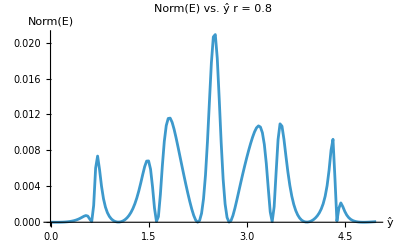

Evaluation time: 16.986639

```mathematica
start=AbsoluteTime[];
r=0.8;

yHat2Array=Range[0,5,0.03];
(*Δ2ReArray={};
Δ2ImArray={};*)
Δ2NormArray={};
For[i=1,i<=Length[yHat2Array],i++,
(*AppendTo[Δ2ReArray,Δ2Re[κ]/.(Join[interiorCoeffs,{yHat->yHat2Array[[i]]}])];
AppendTo[Δ2ImArray,Δ2Im[κ]/.(Join[interiorCoeffs,{yHat->yHat2Array[[i]]}])];*)
AppendTo[Δ2NormArray,Δ2Norm[κ]/.(Join[interiorCoeffs,{yHat->yHat2Array[[i]]}])];
]

(*ERe2Array={};
EIm2Array={};*)
ENorm2Array={};
For[i=1,i<=Length[yHat2Array],i++,
(*AppendTo[ERe2Array,NIntegrate[Δ2ReArray[[i]],{κ,0,r*π}]];
AppendTo[EIm2Array,NIntegrate[Δ2ImArray[[i]],{κ,0,r*π}]];*)
AppendTo[ENorm2Array,NIntegrate[Δ2NormArray[[i]],{κ,0,r*π}]];
]

(*ListPlot[Transpose@{yHat2Array,ERe2Array},Joined->True,PlotLabel->StringJoin["Re(E) vs. ŷ\nr = ",ToString[r]],AxesLabel->{"ŷ","Re(E)"}]
ListPlot[Transpose@{yHat2Array,EIm2Array},Joined->True,PlotLabel->StringJoin["Im(E) vs. ŷ\nr = ",ToString[r]],AxesLabel->{"ŷ","Im(E)"}]*)
ListPlot[Transpose@{yHat2Array,ENorm2Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]
(*Export[StringJoin["r",ToString[r],".png"],%];*)

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

#### 3D Plot of E(ŷ,r)

```mathematica
Clear[r]

yHat2Array=Range[0,5,0.05];
rArray=Range[0.75,0.95,0.0125];
Δ2NormArray={};
For[i=1,i<=Length[yHat2Array],i++,
AppendTo[Δ2NormArray,Δ2Norm[κ]/.(Join[interiorCoeffs,{yHat->yHat2Array[[i]]}])]
;
]

start=AbsoluteTime[];

ENorm2Array=Table[NIntegrate[Δ2NormArray[[i]],{κ,0,rArray[[j]]*π}],{i,Length[yHat2Array]},{j,Length[rArray]}];

plotArray=Flatten[Table[{yHat2Array[[i]],rArray[[j]],ENorm2Array[[i,j]]},{i,Length[yHat2Array]},{j,Length[rArray]}],1];

ListPlot3D[plotArray,PlotLabel->StringJoin["Norm(E) vs. ŷ and r"],AxesLabel->{"ŷ","r","Norm(E)"},Mesh->None,PlotRange->All]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

-Graphics3D-

Evaluation time: 94.4515574

### Node 1

```mathematica
𝔸1[κ_]=γ10+Cos[κ]+γ12 Cos[2 κ]+γ13 Cos[3 κ];
𝔹1[κ_]=Sin[κ]+γ12 Sin[2 κ]+γ13 Sin[3 κ];
ℂ1[κ_]=a10+a21 Cos[κ]+a12 Cos[2 κ]+a13 Cos[3 κ]+a14 Cos[4 κ]+a15 Cos[5 κ]+a16 Cos[6 κ];
𝔻1[κ_]=a11 Sin[κ]+a12 Sin[2 κ]+a13 Sin[3 κ]+a14 Sin[4 κ]+a15 Sin[5 κ]+a16 Sin[6 κ];
κBar1Re[κ_]=(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Im[κ_]=(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Norm[κ_]=Abs[κBar1Re[κ]+I*κBar1Im[κ]];
```

```mathematica
Δ1Re[κ_]=(κ*((𝔸1[κ])^2+(𝔹1[κ])^2)-(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ]))^2;
Δ1Im[κ_]=(κ*((𝔸1[κ])^2+(𝔹1[κ])^2)-(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ]))^2;
Δ1Norm[κ_]=(κ-κBar1Norm[κ])^2;
```

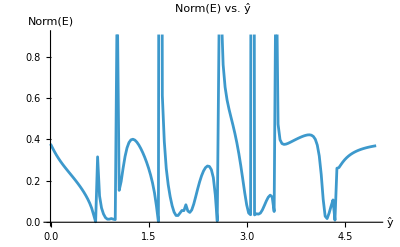

Evaluation time: 133.936822

```mathematica
start=AbsoluteTime[];
r=0.8;

yHat1Array=Range[0,5,0.03];
(*Δ2ReArray={};
Δ2ImArray={};*)
Δ1NormArray={};
For[i=1,i<=Length[yHat1Array],i++,
(*AppendTo[Δ1ReArray,Δ1Re[κ]/.(Join[interiorCoeffs,{yHat->yHat1Array[[i]]}])];
AppendTo[Δ1ImArray,Δ1Im[κ]/.(Join[interiorCoeffs,{yHat->yHat1Array[[i]]}])];*)
AppendTo[Δ1NormArray,Δ1Norm[κ]/.(Join[interiorCoeffs,{yHat->yHat1Array[[i]]}])];
]

(*ERe1Array={};
EIm1Array={};*)
ENorm1Array={};
For[i=1,i<=Length[yHat1Array],i++,
(*AppendTo[ERe1Array,NIntegrate[Δ1ReArray[[i]],{κ,0,0.8*π}]];
AppendTo[EIm1Array,NIntegrate[Δ1ImArray[[i]],{κ,0,0.8*π}]];*)
AppendTo[ENorm1Array,NIntegrate[Δ1NormArray[[i]],{κ,0,0.8*π}]];
]

(*ListPlot[Transpose@{yHat1Array,ERe1Array},Joined->True,PlotLabel->"Re(E) vs. ŷ",AxesLabel->{"ŷ","Re(E)"}]
ListPlot[Transpose@{yHat1Array,EIm1Array},Joined->True,PlotLabel->"Im(E) vs. ŷ",AxesLabel->{"ŷ","Im(E)"}]*)
ListPlot[Transpose@{yHat1Array,ENorm1Array},Joined->True,PlotLabel->"Norm(E) vs. ŷ",AxesLabel->{"ŷ","Norm(E)"}]
(*Export[StringJoin["r",ToString[r],".png"],%];*)

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 0

```mathematica
𝔸0[κ_]=γ00+γ01 Cos[κ]+γ02 Cos[2 κ];
𝔹0[κ_]=γ01 Sin[κ]+γ02 Sin[2 κ];
ℂ0[κ_]=a00+a01 Cos[κ]+a02 Cos[2 κ]+a03 Cos[3 κ]+a04 Cos[4 κ]+a05 Cos[5 κ]+a06 Cos[6 κ];
𝔻0[κ_]=a01 Sin[κ]+a02 Sin[2 κ]+a03 Sin[3 κ]+a04 Sin[4 κ]+a05 Sin[5 κ]+a06 Sin[6 κ];
κBar0Re[κ_]=(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Im[κ_]=(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Norm[κ_]=Abs[κBar0Re[κ]+I*κBar0Im[κ]];
```

```mathematica
Δ0Re[κ_]=(κ*((𝔸0[κ])^2+(𝔹0[κ])^2)-(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ]))^2;
Δ0Im[κ_]=(κ*((𝔸0[κ])^2+(𝔹0[κ])^2)-(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ]))^2;
Δ0Norm[κ_]=(κ-κBar0Norm[κ])^2;
```

```mathematica
start=AbsoluteTime[];
r=0.8;

yHat0Array=Range[0,5,1];
yHat0Array={2.97};
```

```mathematica
Δ0Norm[κ]/.(Join[interiorCoeffs,{yHat->2.97}])
```

(κ-Abs[(-((-3.86926-15.3414 Cos[κ]+12.8836 Cos[2 κ]+7.71726 Cos[3 κ]-1.68413 Cos[4 κ]+0.329338 Cos[5 κ]-0.0354703 Cos[6 κ]) (11.7206 Sin[κ]+15.5545 Sin[2 κ]))+(1+11.7206 Cos[κ]+15.5545 Cos[2 κ]) (-15.3414 Sin[κ]+12.8836 Sin[2 κ]+7.71726 Sin[3 κ]-1.68413 Sin[4 κ]+0.329338 Sin[5 κ]-0.0354703 Sin[6 κ]))/((1+11.7206 Cos[κ]+15.5545 Cos[2 κ])^2+(11.7206 Sin[κ]+15.5545 Sin[2 κ])^2)+(ⅈ ((-1-11.7206 Cos[κ]-15.5545 Cos[2 κ]) (-3.86926-15.3414 Cos[κ]+12.8836 Cos[2 κ]+7.71726 Cos[3 κ]-1.68413 Cos[4 κ]+0.329338 Cos[5 κ]-0.0354703 Cos[6 κ])-(11.7206 Sin[κ]+15.5545 Sin[2 κ]) (-15.3414 Sin[κ]+12.8836 Sin[2 κ]+7.71726 Sin[3 κ]-1.68413 Sin[4 κ]+0.329338 Sin[5 κ]-0.0354703 Sin[6 κ])))/((1+11.7206 Cos[κ]+15.5545 Cos[2 κ])^2+(11.7206 Sin[κ]+15.5545 Sin[2 κ])^2)])^2

```mathematica
NIntegrate[%,{κ,0,0.8*π}]
```

0.00244152

```mathematica
(*Δ2ReArray={};
Δ2ImArray={};*)
(*Δ0NormArray={};
For[i=1,i<=Length[yHat0Array],i++,
(*AppendTo[Δ0ReArray,Δ0Re[κ]/.(Join[interiorCoeffs,{yHat->yHat0Array[[i]]}])];
AppendTo[Δ0ImArray,Δ0Im[κ]/.(Join[interiorCoeffs,{yHat->yHat0Array[[i]]}])];*)
AppendTo[Δ0NormArray,Δ0Norm[κ]/.(Join[interiorCoeffs,{yHat->yHat0Array[[i]]}])];
]*)
Δ0NormArray=ParallelTable[Δ0Norm[κ]/.(Join[interiorCoeffs,{yHat->yHat0Array[[i]]}]),{i,1,Length[yHat0Array]}];
```

```mathematica
(*ERe0Array={};
EIm0Array={};*)
(*ENorm0Array={};
For[i=1,i<=Length[yHat0Array],i++,
(*AppendTo[ERe0Array,NIntegrate[Δ0ReArray[[i]],{κ,0,0.8*π}]];
AppendTo[EIm0Array,NIntegrate[Δ0ImArray[[i]],{κ,0,0.8*π}]];*)
AppendTo[ENorm0Array,NIntegrate[Δ0NormArray[[i]],{κ,0,0.8*π}]];
]*)
ENorm0Array=ParallelTable[NIntegrate[Δ0NormArray[[i]],{κ,0,0.8*π}],{i,1,Length[yHat0Array]}];
```

```mathematica
(*ListPlot[Transpose@{yHat0Array,ERe0Array},Joined->True,PlotLabel->"Re(E) vs. ŷ",AxesLabel->{"ŷ","Re(E)"}]
ListPlot[Transpose@{yHat0Array,EIm0Array},Joined->True,PlotLabel->"Im(E) vs. ŷ",AxesLabel->{"ŷ","Im(E)"}]*)
ListPlot[Transpose@{yHat0Array,ENorm0Array},Joined->True,PlotLabel->"Norm(E) vs. ŷ",AxesLabel->{"ŷ","Norm(E)"}]
(*Export[StringJoin["r",ToString[r],".png"],%];*)

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

## Spectral Function

### Node 2

```mathematica
SF2Re[κ_,yHat_]=κBar2Re[κ]/.interiorCoeffs;
SF2Im[κ_,yHat_]=κBar2Im[κ]/.interiorCoeffs;
SF2Norm[κ_,yHat_]=κBar2Norm[κ]/.interiorCoeffs;
```

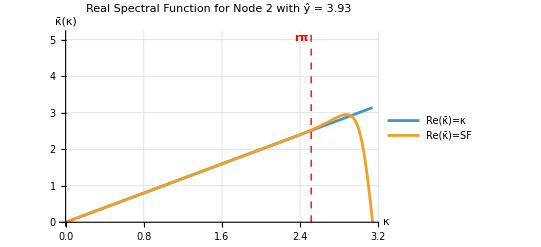

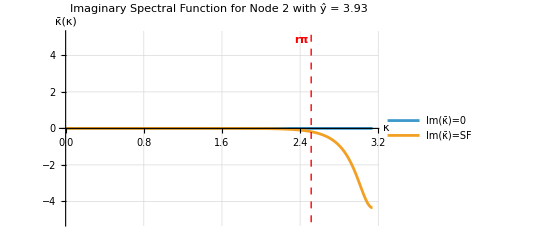

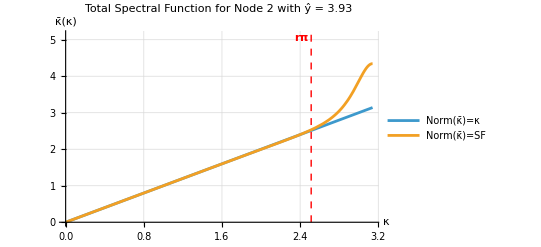

```mathematica
rCor=0.8;
y=3.93;
Plot[{κ,SF2Re[κ,y]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 2 with\n","ŷ = ",ToString[y]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{rCor*π,0},{rCor*π,π+2}}],Text[Style["rπ",Bold],{rCor*π-0.1,π+1.9}]}]
Plot[{0,SF2Im[κ,y]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 2 with\n","ŷ = ",ToString[y]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{rCor*π,-π-2},{rCor*π,π+2}}],Text[Style["rπ",Bold],{rCor*π-0.1,π+1.7}]}]
Plot[{κ,SF2Norm[κ,y]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 2 with\n","ŷ = ",ToString[y]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{rCor*π,0},{rCor*π,π+2}}],Text[Style["rπ",Bold],{rCor*π-0.1,π+1.9}]}]
```

```mathematica
start=AbsoluteTime[];

rCor=0.8;
SFNode2Re=ParallelTable[Plot[{κ,SF2Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{rCor*π,0},{rCor*π,π+2}}],Text[Style["rπ",Bold],{rCor*π-0.1,π+1.9}]}],{yHat,0,5,0.02}];
Export["BD_Node2_Re_ref.gif",SFNode2Re,AnimationRate->10];

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

Evaluation time: 74.2815575

```mathematica
start=AbsoluteTime[];

SFNode2Im=ParallelTable[Plot[{0,SF2Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{rCor*π,-π-2},{rCor*π,π+2}}],Text[Style["rπ",Bold],{rCor*π-0.1,π+1.7}]}],{yHat,0,5,0.02}];
Export["BD_Node2_Im_ref.gif",SFNode2Im,AnimationRate->10];

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

Evaluation time: 100.142415

```mathematica
start=AbsoluteTime[];

SFNode2Norm=ParallelTable[Plot[{κ,SF2Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{rCor*π,0},{rCor*π,π+2}}],Text[Style["rπ",Bold],{rCor*π-0.1,π+1.9}]}],{yHat,0,5,0.02}];
Export["BD_Node2_Norm_ref.gif",SFNode2Norm,AnimationRate->10];

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

Evaluation time: 89.7958833

### Node 1

```mathematica
SF1Re[κ_,yHat_]=κBar1Re[κ]/.interiorCoeffs;
SF1Im[κ_,yHat_]=κBar1Im[κ]/.interiorCoeffs;
SF1Norm[κ_,yHat_]=κBar1Norm[κ]/.interiorCoeffs;
```

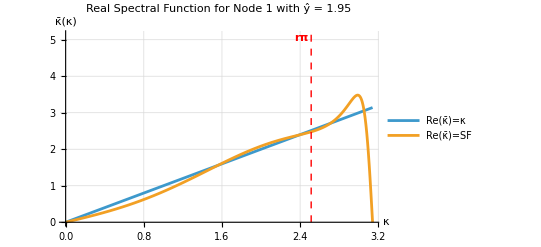

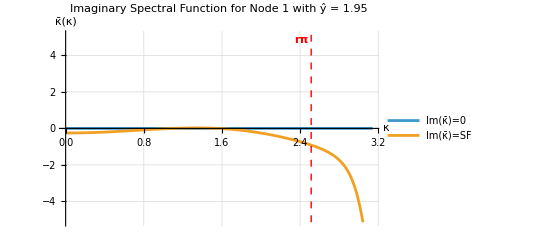

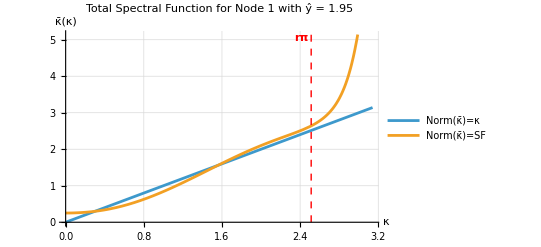

```mathematica
rCor=0.8;
y=1.95;
Plot[{κ,SF1Re[κ,y]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 1 with\n","ŷ = ",ToString[y]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{rCor*π,0},{rCor*π,π+2}}],Text[Style["rπ",Bold],{rCor*π-0.1,π+1.9}]}]
Plot[{0,SF1Im[κ,y]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 1 with\n","ŷ = ",ToString[y]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{rCor*π,-π-2},{rCor*π,π+2}}],Text[Style["rπ",Bold],{rCor*π-0.1,π+1.7}]}]
Plot[{κ,SF1Norm[κ,y]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 1 with\n","ŷ = ",ToString[y]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{rCor*π,0},{rCor*π,π+2}}],Text[Style["rπ",Bold],{rCor*π-0.1,π+1.9}]}]
```

```mathematica
start=AbsoluteTime[];

rCor=0.8;
SFNode1Re=ParallelTable[Plot[{κ,SF1Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{rCor*π,0},{rCor*π,π+2}}],Text[Style["rπ",Bold],{rCor*π-0.1,π+1.9}]}],{yHat,-5,5,0.1}];
Export["BD_Node1_Re.gif",SFNode1Re,AnimationRate->10];

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

```mathematica
start=AbsoluteTime[];

SFNode1Im=ParallelTable[Plot[{0,SF1Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{rCor*π,-π-2},{rCor*π,π+2}}],Text[Style["rπ",Bold],{rCor*π-0.1,π+1.7}]}],{yHat,-5,5,0.1}];
Export["BD_Node1_Im.gif",SFNode1Im,AnimationRate->10];

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

```mathematica
start=AbsoluteTime[];

SFNode1Norm=ParallelTable[Plot[{κ,SF1Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{rCor*π,0},{rCor*π,π+2}}],Text[Style["rπ",Bold],{rCor*π-0.1,π+1.9}]}],{yHat,-5,5,0.1}];
Export["BD_Node1_Norm.gif",SFNode1Norm,AnimationRate->10];

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 0

```mathematica
SF0Re[κ_,yHat_]=κBar0Re[κ]/.interiorCoeffs;
SF0Im[κ_,yHat_]=κBar0Im[κ]/.interiorCoeffs;
SF0Norm[κ_,yHat_]=κBar0Norm[κ]/.interiorCoeffs;
```

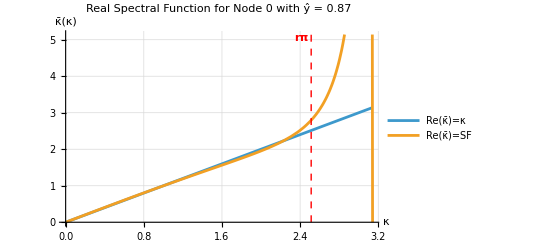

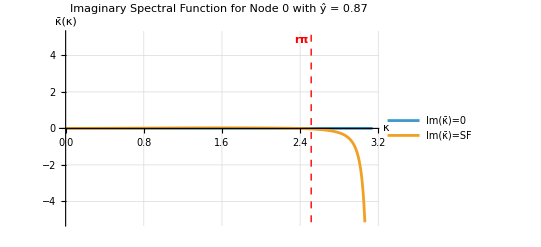

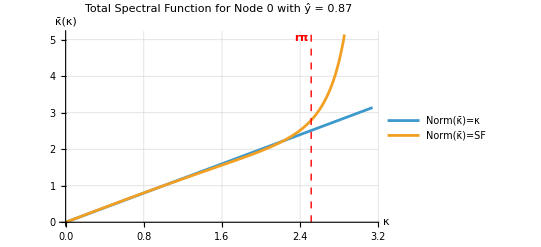

```mathematica
rCor=0.8;
y=0.87;
Plot[{κ,SF0Re[κ,y]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 0 with\n","ŷ = ",ToString[y]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{rCor*π,0},{rCor*π,π+2}}],Text[Style["rπ",Bold],{rCor*π-0.1,π+1.9}]}]
Plot[{0,SF0Im[κ,y]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 0 with\n","ŷ = ",ToString[y]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{rCor*π,-π-2},{rCor*π,π+2}}],Text[Style["rπ",Bold],{rCor*π-0.1,π+1.7}]}]
Plot[{κ,SF0Norm[κ,y]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 0 with\n","ŷ = ",ToString[y]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{rCor*π,0},{rCor*π,π+2}}],Text[Style["rπ",Bold],{rCor*π-0.1,π+1.9}]}]
```

```mathematica
start=AbsoluteTime[];

rCor=0.8;
SFNode0Re=ParallelTable[Plot[{κ,SF0Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{rCor*π,0},{rCor*π,π+2}}],Text[Style["rπ",Bold],{rCor*π-0.1,π+1.9}]}],{yHat,-5,5,0.1}];
Export["BD_Node0_Re.gif",SFNode0Re,AnimationRate->10];

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

Evaluation time: 148.275065

```mathematica
start=AbsoluteTime[];

SFNode0Im=ParallelTable[Plot[{0,SF0Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{rCor*π,-π-2},{rCor*π,π+2}}],Text[Style["rπ",Bold],{rCor*π-0.1,π+1.7}]}],{yHat,-5,5,0.1}];
Export["BD_Node0_Im.gif",SFNode0Im,AnimationRate->10];

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

Evaluation time: 162.994232

```mathematica
start=AbsoluteTime[];

SFNode0Norm=ParallelTable[Plot[{κ,SF0Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{rCor*π,0},{rCor*π,π+2}}],Text[Style["rπ",Bold],{rCor*π-0.1,π+1.9}]}],{yHat,-5,5,0.1}];
Export["BD_Node0_Norm.gif",SFNode0Norm,AnimationRate->10];

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

Evaluation time: 237.338238

## Output Coefficients

```mathematica
Clear[α,β,a1,a2,a3,yHat2,yHat1,yHat0,yHat]
Clear[γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]
```

```mathematica
yHat2List={(*1*)0.2,(*2*)0.63,(*3*)1.05,(*4*)1.14,(*5*)1.62,(*6*)2.25,(*7*)2.73,(*8*)3.39,(*9*)3.93,(*10*)4.38,(*11*)4.80};
yHat1List={(*1*)0.69,(*2*)0.99,(*3*)1.65,(*4*)1.95,(*5*)2.13,(*6*)2.55,(*7*)3.06,(*8*)3.12,(*9*)3.42,(*10*)4.23,(*11*)4.35};
yHat0List={(*1*)0.87,(*2*)1.89,(*3*)2.97,(*4*)4.17,(*5*)4.26};

yHat2=yHat2List[[9]];
yHat1=yHat1List[[4]];
yHat0=yHat0List[[1]];
```

### Definition and String Output

```mathematica
γ22val=γ22/.{bdCoeffs2[[3]]/.interiorCoeffs};
γ20val=1/γ22val*(γ20/.{bdCoeffs2[[1]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
γ21val=1/γ22val*(γ21/.{bdCoeffs2[[2]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
γ23val=1/γ22val*(γ23/.{bdCoeffs2[[4]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
γ24val=1/γ22val*(γ24/.{bdCoeffs2[[5]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
a20val=1/γ22val*(a20/.{bdCoeffs2[[6]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
a21val=1/γ22val*(a21/.{bdCoeffs2[[7]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
a22val=1/γ22val*(a22/.{bdCoeffs2[[8]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
a23val=1/γ22val*(a23/.{bdCoeffs2[[9]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
a24val=1/γ22val*(a24/.{bdCoeffs2[[10]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
a25val=1/γ22val*(a25/.{bdCoeffs2[[11]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
a26val=1/γ22val*(a26/.{bdCoeffs2[[12]]/.(Join[interiorCoeffs,{yHat->yHat2}])})/.{yHat->yHat2};
γ22val=γ22val/γ22val/.{yHat->yHat2};



γ11val=γ11/.{bdCoeffs1[[2]]/.interiorCoeffs};
γ10val=1/γ11val*(γ10/.{bdCoeffs1[[1]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
γ12val=1/γ11val*(γ12/.{bdCoeffs1[[3]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
γ13val=1/γ11val*(γ13/.{bdCoeffs1[[4]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
a10val=1/γ11val*(a10/.{bdCoeffs1[[5]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
a11val=1/γ11val*(a11/.{bdCoeffs1[[6]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
a12val=1/γ11val*(a12/.{bdCoeffs1[[7]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
a13val=1/γ11val*(a13/.{bdCoeffs1[[8]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
a14val=1/γ11val*(a14/.{bdCoeffs1[[9]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
a15val=1/γ11val*(a15/.{bdCoeffs1[[10]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
a16val=1/γ11val*(a16/.{bdCoeffs1[[11]]/.(Join[interiorCoeffs,{yHat->yHat1}])})/.{yHat->yHat1};
γ11val=γ11val/γ11val/.{yHat->yHat1};



γ00val=γ00/.{bdCoeffs0[[1]]/.interiorCoeffs};
γ01val=1/γ00val*(γ01/.{bdCoeffs0[[2]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
γ02val=1/γ00val*(γ02/.{bdCoeffs0[[3]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
a00val=1/γ00val*(a00/.{bdCoeffs0[[4]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
a01val=1/γ00val*(a01/.{bdCoeffs0[[5]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
a02val=1/γ00val*(a02/.{bdCoeffs0[[6]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
a03val=1/γ00val*(a03/.{bdCoeffs0[[7]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
a04val=1/γ00val*(a04/.{bdCoeffs0[[8]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
a05val=1/γ00val*(a05/.{bdCoeffs0[[9]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
a06val=1/γ00val*(a06/.{bdCoeffs0[[10]]/.(Join[interiorCoeffs,{yHat->yHat0}])})/.{yHat->yHat0};
γ00val=γ00val/γ00val/.{yHat->yHat0};

Print[StringJoin[
"LHS Parameters:",
"\nγ_01 = ",ToString[γ01val],
"\nγ_02 = ",ToString[γ02val],
"\nγ_10 = ",ToString[γ10val],
"\nγ_12 = ",ToString[γ12val],
"\nγ_13 = ",ToString[γ13val],
"\nγ_20 = ",ToString[γ20val],
"\nγ_21 = ",ToString[γ21val],
"\nγ_23 = ",ToString[γ23val],
"\nγ_24 = ",ToString[γ24val]
]]

Print[StringJoin[
"RHS Parameters:",
"\na_00 = ",ToString[a00val],
"\na_01 = ",ToString[a01val],
"\na_02 = ",ToString[a02val],
"\na_03 = ",ToString[a03val],
"\na_04 = ",ToString[a04val],
"\na_05 = ",ToString[a05val],
"\na_06 = ",ToString[a06val],
"\na_10 = ",ToString[a10val],
"\na_11 = ",ToString[a11val],
"\na_12 = ",ToString[a12val],
"\na_13 = ",ToString[a13val],
"\na_14 = ",ToString[a14val],
"\na_15 = ",ToString[a15val],
"\na_16 = ",ToString[a16val],
"\na_20 = ",ToString[a20val],
"\na_21 = ",ToString[a21val],
"\na_22 = ",ToString[a22val],
"\na_23 = ",ToString[a23val],
"\na_24 = ",ToString[a24val],
"\na_25 = ",ToString[a25val],
"\na_26 = ",ToString[a26val]
]]
```

LHS Parameters:
γ_01 = 7.38238
γ_02 = 6.11839
γ_10 = 0.108107
γ_12 = 0.987942
γ_13 = -0.019091
γ_20 = 0.0108325
γ_21 = 0.238187
γ_23 = 1.12828
γ_24 = 0.28865

RHS Parameters:
a_00 = -3.43876
a_01 = -6.12097
a_02 = 7.81928
a_03 = 2.03271
a_04 = -0.357834
a_05 = 0.0770426
a_06 = -0.0114698
a_10 = -0.396496
a_11 = -1.04205
a_12 = 1.14708
a_13 = 0.349408
a_14 = -0.06738
a_15 = 0.0105042
a_16 = -0.00106238
a_20 = -0.0467869
a_21 = -0.510448
a_22 = -0.770033
a_23 = 0.622893
a_24 = 0.672713
a_25 = 0.0330417
a_26 = -0.00137935

### Luke Output

```mathematica
interior={α->0.5770460201292381,β->0.08900836845092142,a->0.6517078440898839,b->0.24815882627035918,c->0.006009630649852392};
boundary={α12->γ01val,β12->γ02val,α21->γ10val,α22->γ12val,β22->γ13val,β31->γ20val,α31->γ21val,α32->γ23val,β32->γ24val,a1->a00val,b1->a01val,c1->a02val,d1->a03val,e1->a04val,f1->a05val,g1->a06val,a2->a10val,b2->a11val,c2->a12val,d2->a13val,e2->a14val,f2->a15val,g2->a16val,a3->a20val,b3->a21val,c3->a22val,d3->a23val,e3->a24val,f3->a25val,g3->a26val};
coeff=Flatten[Join[interior,boundary]]
```

{α→0.577046,β→0.0890084,a→0.651708,b→0.248159,c→0.00600963,α12→11.7206,β12→15.5545,α21→0.105117,α22→1.39996,β22→0.366268,β31→0.0248623,α31→0.368641,α32→0.754761,β32→0.143779,a1→-3.86926,b1→-15.3414,c1→12.8836,d1→7.71726,e1→-1.68413,f1→0.329338,g1→-0.0354703,a2→-0.380754,b2→-1.17303,c2→0.653694,d2→0.862787,e2→0.0373594,f2→0.000448634,g2→-0.000509666,a3→-0.098818,b3→-0.631836,c3→-0.338327,d3→0.688717,e3→0.366244,f3→0.014715,g3→-0.000694483}

```mathematica
Kim24={α->0.5862704032801503,β->0.0954953355017055,a->0.6431406736919156,b->0.2586011023495066,c->0.007140953479797375,α12->43.65980335321481,β12->92.40143116322876,α21->0.08351537442980239,α22->1.961483362670730,β22->0.8789761422182460,β31->0.008073091519768687,α31->0.2162434143850924,α32->1.052242062502679,β32->0.2116022463346598,a1->-6.658527037451025,b1->-86.92242000231872,c1->47.58661913475775,d1->57.30693626084370,e1->-13.71254216556246,f1->2.659826729790792,g1->-0.2598929200600359,a2->-0.3199960780333493,b2->-1.438068456255548,c2->0.07735499170041915,d2->1.496612372811008,e2->0.2046919801608821,f2->-0.02229717539815850,g2->0.001702365014746567,a3->-0.03644974757120792,b3->-0.4997030280694729,c3->-0.7861024376433451,d3->0.7439822445654316,e3->0.5629384925762924,f3->0.01563884275691290,g3->-0.0003043666146108995};
HAMR={α->0.5747612151,β->0.0879324249,a->1.3069171114/2,b->0.9828406281/4,c->0.0356295405/6,α12->9.4133049605,β12->10.7741034803,α21->0.1023343303,α22->1.8854940182,β22->0.8582327249,β31->0.0347468867,α31->0.4064246796,α32->0.7683583302,β32->0.1623349133,a1->-3.6882535854000005,b1->-10.3169611301,c1->9.6807767746,d1->5.4529053045,e1->-1.5191959829,f1->0.4834876759,g1->-0.0927590566,a2->-0.3586079596,b2->-1.3424668425,c2->0.0834751059,d2->1.4235697122,e2->0.2245783548,f2->-0.0358453729,g2->0.0052970021,a3->-0.1274311870,b3->-0.6299599564,c3->-0.3024922988999999,d3->0.6498856630,e3->0.3919470424,f3->0.0189402158,g3->-0.0008894789};
coeff=Kim24;
```

### My Output

```mathematica
interior={α->0.5770460201292381,β->0.08900836845092142,a1->0.6517078440898839,a2->0.24815882627035918,a3->0.006009630649852392};
boundary={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeff=Flatten[Join[interior,boundary]]
```

{α→0.577046,β→0.0890084,a1→0.651708,a2→0.248159,a3→0.00600963,γ01→7.38238,γ02→6.11839,γ10→0.108107,γ12→0.987942,γ13→-0.019091,γ20→0.0108325,γ21→0.238187,γ23→1.12828,γ24→0.28865,a00→-3.43876,a01→-6.12097,a02→7.81928,a03→2.03271,a04→-0.357834,a05→0.0770426,a06→-0.0114698,a10→-0.396496,a11→-1.04205,a12→1.14708,a13→0.349408,a14→-0.06738,a15→0.0105042,a16→-0.00106238,a20→-0.0467869,a21→-0.510448,a22→-0.770033,a23→0.622893,a24→0.672713,a25→0.0330417,a26→-0.00137935}

### Kim 07 Modified Boundary Coefficients

Why is Kim 07 different than HAMR for modifying the coeffs for eigenvalue analysis? (eqs 41-45)

```mathematica
Kim07={α->0.5862704032801503,β->0.0954953355017055,a1->0.6431406736919156,a2->0.2586011023495066,a3->0.007140953479797375,γ01->5.912678614078549,γ02->3.775623951744012,γ10->0.08360703307833438,γ12->2.058102869495757,γ13->0.9704052014790193,γ20->0.03250008295108466,γ21->0.3998040493524358,γ23->0.7719261277615860,γ24->0.1626635931256900,a00->-3.240681563472493,a01->-3.456878182643609,a02->5.839043358834730,a03->1.015886726041007,a04->-0.2246526470654333,a05->0.08564940889936562,a06->-0.01836710059356763,a10->-0.3177447290722621,a11->-1.468827048894462,a12->-0.02807631929593225,a13->1.593461635747659,a14->0.2533027046976367,a15->-0.03619652460174756,a16->0.004080281419108407,a20->-0.1219006056449124,a21->-0.6301651351188667,a22->-0.3119603043096557,a23->0.6521195063966084,a24->0.3938843551210350,a25->0.01904944407973912,a26->-0.001027260523947668};
```

```mathematica
{γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.Kim07),
γ13Bar->(γ13/(1-γ10*γ01)/.Kim07),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.Kim07),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.Kim07),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.Kim07)};

Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.Kim07;
Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.Kim07;

barCoeffs=Join[%,%%,%%%]
```

{a21Bar→-0.296033,a22Bar→-1.50549,a23Bar→0.16354,a24Bar→1.47735,a25Bar→0.165628,a26Bar→-0.0130691,a11Bar→-2.33321,a12Bar→-1.02097,a13Bar→2.98329,a14Bar→0.538081,a15Bar→-0.0857445,a16Bar→0.0111061,γ12Bar→3.44587,γ13Bar→1.91909,γ21Bar→0.0554085,γ23Bar→1.97387,γ24Bar→0.813458}

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.Kim07)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | 0 | 0 | 0 | 0 | 0
β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | γ24 | γ23 | 1 | γ21 | γ20
0 | 0 | 0 | 0 | 0 | γ13 | γ12 | 1 | γ10
0 | 0 | 0 | 0 | 0 | 0 | γ02 | γ01 | 1)

(1 | 3.44587 | 1.91909 | 0 | 0 | 0 | 0 | 0 | 0
0.0554085 | 1 | 1.97387 | 0.813458 | 0 | 0 | 0 | 0 | 0
0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0
0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0
0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0
0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0
0 | 0 | 0 | 0 | 0.162664 | 0.771926 | 1 | 0.399804 | 0.0325001
0 | 0 | 0 | 0 | 0 | 0.970405 | 2.0581 | 1 | 0.083607
0 | 0 | 0 | 0 | 0 | 0 | 3.77562 | 5.91268 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@RHS[k]

MatrixForm@(RHS[k]/.Kim07)/.barCoeffs
```

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | 0 | 0 | 0
-a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0
-a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0
0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0
0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3
0 | 0 | -a26 | -a25 | -a24 | -a23 | -a22 | -a21 | -a20
0 | 0 | -a16 | -a15 | -a14 | -a13 | -a12 | -a11 | -a10
0 | 0 | -a06 | -a05 | -a04 | -a03 | -a02 | -a01 | -a00)

(-2.33321 | -1.02097 | 2.98329 | 0.538081 | -0.0857445 | 0.0111061 | 0 | 0 | 0
-0.296033 | -1.50549 | 0.16354 | 1.47735 | 0.165628 | -0.0130691 | 0 | 0 | 0
-0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0
-0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0
0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0
0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095
0 | 0 | 0.00102726 | -0.0190494 | -0.393884 | -0.65212 | 0.31196 | 0.630165 | 0.121901
0 | 0 | -0.00408028 | 0.0361965 | -0.253303 | -1.59346 | 0.0280763 | 1.46883 | 0.317745
0 | 0 | 0.0183671 | -0.0856494 | 0.224653 | -1.01589 | -5.83904 | 3.45688 | 3.24068)

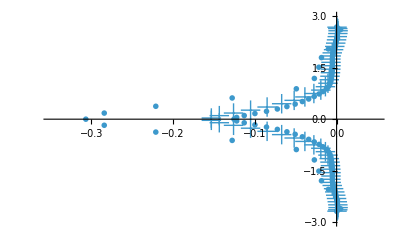

```mathematica
k=21;
LHSNum=(LHS[k]/.Kim07)/.barCoeffs;
RHSNum=(RHS[k]/.Kim07)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n21=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotMarkers->Style["◯",8]];

k=60;
LHSNum=(LHS[k]/.Kim07)/.barCoeffs;
RHSNum=(RHS[k]/.Kim07)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n60=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotMarkers->Style["+",20]];

k=81;
LHSNum=(LHS[k]/.Kim07)/.barCoeffs;
RHSNum=(RHS[k]/.Kim07)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n81=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotMarkers->Style["·",36]];

Show[n21,n60,n81,PlotRange->{{-0.35,0.05},{-3,3}}]
```

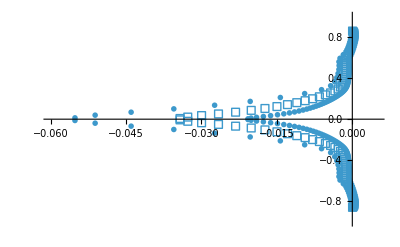

```mathematica
k=50;
LHSNum=(LHS[k]/.Kim07)/.barCoeffs;
RHSNum=(RHS[k]/.Kim07)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat]/π;

n50=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotMarkers->Style["⊲",8]];

k=100;
LHSNum=(LHS[k]/.Kim07)/.barCoeffs;
RHSNum=(RHS[k]/.Kim07)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat]/π;

n100=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotMarkers->Style["□",8]];

k=200;
LHSNum=(LHS[k]/.Kim07)/.barCoeffs;
RHSNum=(RHS[k]/.Kim07)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat]/π;

n200=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotMarkers->Style["◯",6]];

Show[n50,n100,n200,PlotRange->{{-0.06,0.005},{-1,1}}]
```

### Kim 24 Modified Boundary Coefficients

```mathematica
Kim24={α->0.5862704032801503,β->0.0954953355017055,a1->0.6431406736919156,a2->0.2586011023495066,a3->0.007140953479797375,γ01->43.65980335321481,γ02->92.40143116322876,γ10->0.08351537442980239,γ12->1.961483362670730,γ13->0.8789761422182460,γ20->0.008073091519768687,γ21->0.2162434143850924,γ23->1.052242062502679,γ24->0.2116022463346598,a00->-6.658527037451025,a01->-86.92242000231872,a02->47.58661913475775,a03->57.30693626084370,a04->-13.71254216556246,a05->2.659826729790792,a06->-0.2598929200600359,a10->-0.3199960780333493,a11->-1.438068456255548,a12->0.07735499170041915,a13->1.496612372811008,a14->0.2046919801608821,a15->-0.02229717539815850,a16->0.001702365014746567,a20->-0.03644974757120792,a21->-0.4997030280694729,a22->-0.7861024376433451,a23->0.7439822445654316,a24->0.5629384925762924,a25->0.01563884275691290,a26->-0.0003043666146108995};
```

```mathematica
{γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.Kim24),
γ13Bar->(γ13/(1-γ10*γ01)/.Kim24),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.Kim24),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.Kim24),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.Kim24)};

Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.Kim24;
Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.Kim24;

barCoeffs=Join[%,%%,%%%]
```

{a21Bar→-0.445082,a22Bar→-0.979255,a23Bar→0.739533,a24Bar→0.670234,a25Bar→0.0219576,a26Bar→-0.000578643,a11Bar→-2.19981,a12Bar→1.47259,a13Bar→1.24303,a14Bar→-0.510115,a15Bar→0.0923693,a16Bar→-0.00884546,γ12Bar→2.17494,γ13Bar→-0.332157,γ21Bar→0.147555,γ23Bar→1.19359,γ24Bar→0.261111}

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.Kim24)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | 0 | 0 | 0 | 0 | 0
β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | γ24 | γ23 | 1 | γ21 | γ20
0 | 0 | 0 | 0 | 0 | γ13 | γ12 | 1 | γ10
0 | 0 | 0 | 0 | 0 | 0 | γ02 | γ01 | 1)

(1 | 2.17494 | -0.332157 | 0 | 0 | 0 | 0 | 0 | 0
0.147555 | 1 | 1.19359 | 0.261111 | 0 | 0 | 0 | 0 | 0
0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0
0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0
0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0
0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0
0 | 0 | 0 | 0 | 0.211602 | 1.05224 | 1 | 0.216243 | 0.00807309
0 | 0 | 0 | 0 | 0 | 0.878976 | 1.96148 | 1 | 0.0835154
0 | 0 | 0 | 0 | 0 | 0 | 92.4014 | 43.6598 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@RHS[k]
```

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | 0 | 0 | 0
-a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0
-a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0
0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0
0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3
0 | 0 | -a26 | -a25 | -a24 | -a23 | -a22 | -a21 | -a20
0 | 0 | -a16 | -a15 | -a14 | -a13 | -a12 | -a11 | -a10
0 | 0 | -a06 | -a05 | -a04 | -a03 | -a02 | -a01 | -a00)

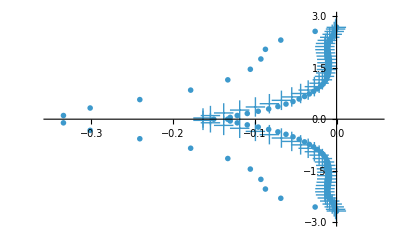

```mathematica
k=21;
LHSNum=(LHS[k]/.Kim24)/.barCoeffs;
RHSNum=(RHS[k]/.Kim24)/.barCoeffs;
RHSNum[[All,1]]=RHSNum[[All,1]]*(1-r)/.{r->0.7};

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n21=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{{-0.35,0.05},{-3,3}},PlotMarkers->Style["◯",8]];

k=60;
LHSNum=(LHS[k]/.Kim24)/.barCoeffs;
RHSNum=(RHS[k]/.Kim24)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n60=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{{-0.35,0.05},{-3,3}},PlotMarkers->Style["+",20]];

k=81;
LHSNum=(LHS[k]/.Kim24)/.barCoeffs;
RHSNum=(RHS[k]/.Kim24)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n81=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{{-0.35,0.05},{-3,3}},PlotMarkers->Style["·",36]];

Show[n21,n60,n81]
```

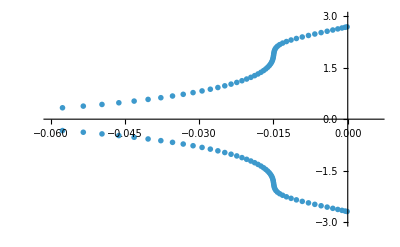

```mathematica
k=121;
LHSNum=(LHS[k]/.Kim24)/.barCoeffs;
RHSNum=(RHS[k]/.Kim24)/.barCoeffs;
RHSNum[[All,1]]=RHSNum[[All,1]]*(1-r)/.{r->0.7};

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{{-0.06,0.006},{-3,3}},PlotMarkers->Style["Δ",8]]
```

```mathematica
LHSBorders={
{1,α12,β12},
{α21,1,α22,β22},
{β31,α31,1,α32,β32}
};
RHSBorders={
{a1,b1,c1,d1,e1,f1,g1},
{a2,b2,c2,d2,e2,f2,g2},
{a3,b3,c3,d3,e3,f3,g3}
};

LHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->1,
Band[{2,1}]->α,
Band[{1,2}]->α,
Band[{3,1}]->β,
Band[{1,3}]->β
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[LHSBorders[[i]]],j++,
M[[i,j]]=LHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=LHSBorders[[i,j]]/.coeff
]
];

M
]

RHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{2,1}]->-a,
Band[{3,1}]->-b,
Band[{4,1}]->-c,
Band[{1,2}]->a,
Band[{1,3}]->b,
Band[{1,4}]->c
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[RHSBorders[[i]]],j++,
M[[i,j]]=RHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=-RHSBorders[[i,j]]/.coeff
]
];

M
]
```

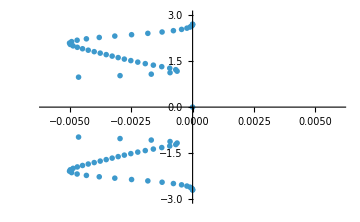

```mathematica
nList={21,60,81};
nList={121};
plotList={};
For[k=1,k<=Length@nList,k++,
n=nList[[k]];
LHS=LHSMatrix[n,3,coeff];
RHS=RHSMatrix[n,3,coeff];
(*Print[MatrixForm@Normal@RHS];*)
RHS[[All,1]]=RHS[[All,1]]*(1-0.7);
(*Print[MatrixForm@Normal@RHS];*)

(*For[j=1,j<=n,j++,LHS[[1,j]]=0];
For[j=1,j<=n,j++,LHS[[j,1]]=0];
For[j=1,j<=n,j++,RHS[[1,j]]=0];
For[j=1,j<=n,j++,RHS[[j,1]]=0];
LHS[[1,1]]=1;*)
(*For[j=1,j<=n,j++,RHS[[1,j]]=0];
For[j=1,j<=n,j++,RHS[[n,j]]=0];
For[j=1,j<=n,j++,RHS[[n-1,j]]=0];*)
LHS//MatrixForm;
RHS//MatrixForm;
(*Print[LHS//MatrixForm];
Print[RHS//MatrixForm];*)

mat=Inverse[LHS].RHS;
eigs=-Eigenvalues[mat];

AppendTo[plotList,ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotMarkers->Style["Δ",8],PlotRange->{{-0.006,0.006},{-3,3}},ImageSize->Medium]]
]
plotList
```

### HAMR 08 Modified Boundary Coefficients

```mathematica
HAMR2={α->0.5747612151,β->0.0879324249,a1->1.3069171114/2,a2->0.9828406281/4,a3->0.0356295405/6,γ01->9.4133049605,γ02->10.7741034803,γ10->0.1023343303,γ12->1.8854940182,γ13->0.8582327249,γ20->0.0347468867,γ21->0.4064246796,γ23->0.7683583302,γ24->0.1623349133,a00->-3.6882535854000005,a01->-10.3169611301,a02->9.6807767746,a03->5.4529053045,a04->-1.5191959829,a05->0.4834876759,a06->-0.0927590566,a10->-0.3586079596,a11->-1.3424668425,a12->0.0834751059,a13->1.4235697122,a14->0.2245783548,a15->-0.0358453729,a16->0.0052970021,a20->-0.1274311870,a21->-0.6299599564,a22->-0.3024922988999999,a23->0.6498856630,a24->0.3919470424,a25->0.0189402158,a26->-0.0008894789};
γ03=0;
γ04=0;
```

```mathematica
{γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.HAMR2),
γ13Bar->((γ13-γ03*γ10)/(1-γ10*γ01)/.HAMR2),
γ21Bar->((γ21-γ01*γ20)/(1-γ20*γ02)/.HAMR2),
γ23Bar->((γ23-γ03*γ20)/(1-γ20*γ02)/.HAMR2),
γ24Bar->((γ24-γ04*γ20)/(1-γ20*γ02)/.HAMR2)};

Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.HAMR2;
Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(1-γ20*γ02)*(ToExpression@StringJoin["a2",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ20),
{j,1,6}]/.HAMR2;

barCoeffs=Join[%,%%,%%%]
```

{a21Bar→-0.433924,a22Bar→-1.02116,a23Bar→0.735917,a24Bar→0.710855,a25Bar→0.00342137,a26Bar→0.00372999,a11Bar→-7.81256,a12Bar→-24.7222,a13Bar→23.5872,a14Bar→10.3566,a15Bar→-2.32514,a16Bar→0.403029,γ12Bar→21.3358,γ13Bar→23.3878,γ21Bar→0.126818,γ23Bar→1.22813,γ24Bar→0.259473}

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.HAMR2)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | 0 | 0 | 0 | 0 | 0
β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | γ24 | γ23 | 1 | γ21 | γ20
0 | 0 | 0 | 0 | 0 | γ13 | γ12 | 1 | γ10
0 | 0 | 0 | 0 | 0 | 0 | γ02 | γ01 | 1)

(1 | 21.3358 | 23.3878 | 0 | 0 | 0 | 0 | 0 | 0
0.126818 | 1 | 1.22813 | 0.259473 | 0 | 0 | 0 | 0 | 0
0.0879324 | 0.574761 | 1 | 0.574761 | 0.0879324 | 0 | 0 | 0 | 0
0 | 0.0879324 | 0.574761 | 1 | 0.574761 | 0.0879324 | 0 | 0 | 0
0 | 0 | 0.0879324 | 0.574761 | 1 | 0.574761 | 0.0879324 | 0 | 0
0 | 0 | 0 | 0.0879324 | 0.574761 | 1 | 0.574761 | 0.0879324 | 0
0 | 0 | 0 | 0 | 0.162335 | 0.768358 | 1 | 0.406425 | 0.0347469
0 | 0 | 0 | 0 | 0 | 0.858233 | 1.88549 | 1 | 0.102334
0 | 0 | 0 | 0 | 0 | 0 | 10.7741 | 9.4133 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@RHS[k]

MatrixForm@(RHS[k]/.HAMR2)/.barCoeffs
```

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | 0 | 0 | 0
-a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0
-a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0
0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0
0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3
0 | 0 | -a26 | -a25 | -a24 | -a23 | -a22 | -a21 | -a20
0 | 0 | -a16 | -a15 | -a14 | -a13 | -a12 | -a11 | -a10
0 | 0 | -a06 | -a05 | -a04 | -a03 | -a02 | -a01 | -a00)

(-7.81256 | -24.7222 | 23.5872 | 10.3566 | -2.32514 | 0.403029 | 0 | 0 | 0
-0.433924 | -1.02116 | 0.735917 | 0.710855 | 0.00342137 | 0.00372999 | 0 | 0 | 0
-0.24571 | -0.653459 | 0 | 0.653459 | 0.24571 | 0.00593826 | 0 | 0 | 0
-0.00593826 | -0.24571 | -0.653459 | 0 | 0.653459 | 0.24571 | 0.00593826 | 0 | 0
0 | -0.00593826 | -0.24571 | -0.653459 | 0 | 0.653459 | 0.24571 | 0.00593826 | 0
0 | 0 | -0.00593826 | -0.24571 | -0.653459 | 0 | 0.653459 | 0.24571 | 0.00593826
0 | 0 | 0.000889479 | -0.0189402 | -0.391947 | -0.649886 | 0.302492 | 0.62996 | 0.127431
0 | 0 | -0.005297 | 0.0358454 | -0.224578 | -1.42357 | -0.0834751 | 1.34247 | 0.358608
0 | 0 | 0.0927591 | -0.483488 | 1.5192 | -5.45291 | -9.68078 | 10.317 | 3.68825)

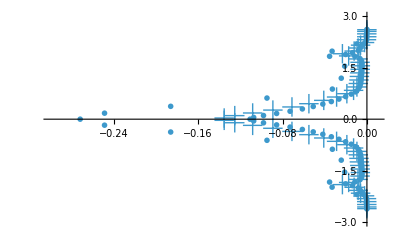

```mathematica
k=21;
LHSNum=(LHS[k]/.HAMR2)/.barCoeffs;
RHSNum=(RHS[k]/.HAMR2)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n21=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{{-0.3,0.01},{-3,3}},PlotMarkers->Style["◯",8]];

k=60;
LHSNum=(LHS[k]/.HAMR2)/.barCoeffs;
RHSNum=(RHS[k]/.HAMR2)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n60=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{{-0.3,0.01},{-3,3}},PlotMarkers->Style["+",20]];

k=81;
LHSNum=(LHS[k]/.HAMR2)/.barCoeffs;
RHSNum=(RHS[k]/.HAMR2)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n81=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{{-0.3,0.01},{-3,3}},PlotMarkers->Style["·",36]];

Show[n21,n60,n81]
```

## Eigenvalue Spectral Analysis

### Old

#### Generate Matrices

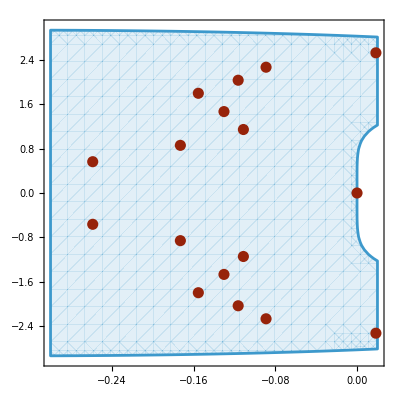

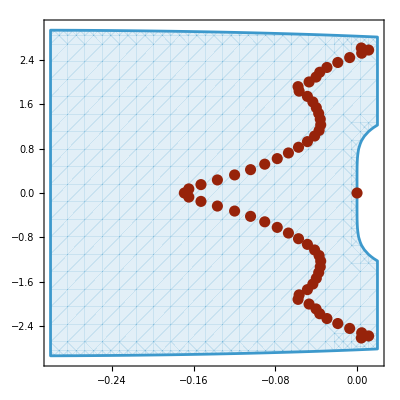

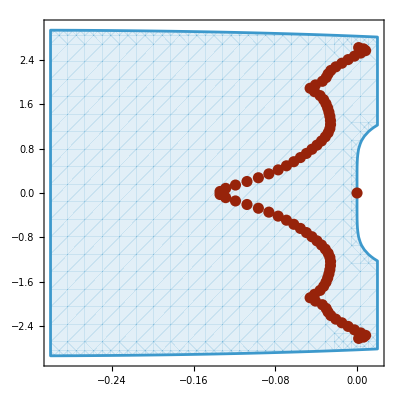

```mathematica
LHSBorders={
{1,α12,β12},
{α21,1,α22,β22},
{β31,α31,1,α32,β32}
};
RHSBorders={
{a1,b1,c1,d1,e1,f1,g1},
{a2,b2,c2,d2,e2,f2,g2},
{a3,b3,c3,d3,e3,f3,g3}
};

LHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->1,
Band[{2,1}]->α,
Band[{1,2}]->α,
Band[{3,1}]->β,
Band[{1,3}]->β
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[LHSBorders[[i]]],j++,
M[[i,j]]=LHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=LHSBorders[[i,j]]/.coeff
]
];

M
]

RHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{2,1}]->-a,
Band[{3,1}]->-b,
Band[{4,1}]->-c,
Band[{1,2}]->a,
Band[{1,3}]->b,
Band[{1,4}]->c
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[RHSBorders[[i]]],j++,
M[[i,j]]=RHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=-RHSBorders[[i,j]]/.coeff
]
];

M
]

nList={80,160,320};
nList={21,60,81};
plotList={};
For[k=1,k<=Length@nList,k++,
n=nList[[k]];
LHS=LHSMatrix[n,3,coeff];
RHS=RHSMatrix[n,3,coeff];

For[j=1,j<=n,j++,LHS[[1,j]]=0];
For[j=1,j<=n,j++,LHS[[j,1]]=0];
For[j=1,j<=n,j++,RHS[[1,j]]=0];
For[j=1,j<=n,j++,RHS[[j,1]]=0];
LHS[[1,1]]=1;
(*For[j=1,j<=n,j++,RHS[[1,j]]=0];
For[j=1,j<=n,j++,RHS[[n,j]]=0];
For[j=1,j<=n,j++,RHS[[n-1,j]]=0];*)
LHS//MatrixForm;
RHS//MatrixForm;
(*Print[LHS//MatrixForm];
Print[RHS//MatrixForm];*)

mat=Inverse[LHS].RHS;
eigs=-Eigenvalues[mat];
AppendTo[plotList,ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[nList[[k]]]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->{RGBColor[yHat0/5,yHat1/5,yHat2/5],PointSize[0.02]}]]
]
rk4StabilityRegion=RegionPlot[(Abs[1+(x+I y)+(x+I y)^2/2+(x+I y)^3/6+(x+I y)^4/24])<1,{x,-3,0.25},{y,-3,3},PlotStyle->Directive[Opacity[0.15]]];
rk4StabilityRegion=RegionPlot[(Abs[1+(x+I y)+(x+I y)^2/2+(x+I y)^3/6+(x+I y)^4/24])<1,{x,-0.3,0.02},{y,-3,3},PlotStyle->Directive[Opacity[0.15]]];
eulerStabilityRegion=RegionPlot[(Abs[1+(x+I y)])<1,{x,-3,0.25},{y,-3,3},PlotStyle->Directive[Opacity[0.15]]];
Show[rk4StabilityRegion,plotList[[1]]]
Show[rk4StabilityRegion,plotList[[2]]]
Show[rk4StabilityRegion,plotList[[3]]]
```

#### Show Eigenvalue Spectra

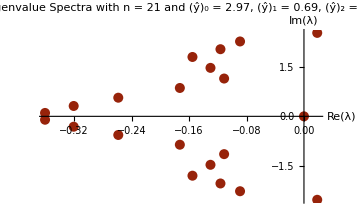
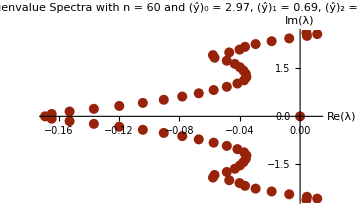
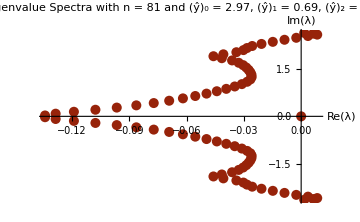

```mathematica
plotList
```

### New

```mathematica
(*This was a scheme I sent Luke and Andrew with Subscript[ŷ, 0]=0.87, Subscript[ŷ, 1]=1.95, Subscript[ŷ, 2]=3.93*)
(*coeff={α->0.577046020129,β->0.0890083684509,a1->0.65170784409,a2->0.24815882627,a3->0.00600963064985,γ01->7.54033708428,γ02->6.68314895992,γ10->0.10810728338,γ12->0.987941528443,γ13->-0.0190910498621,γ20->0.0108325025097,γ21->0.238186806866,γ23->1.12827907699,γ24->0.288649699199,a00->-3.45139624553,a01->-6.50490079826,a02->7.66779401418,a03->2.52842591838,a04->-0.300598774934,a05->0.0717510137605,a06->-0.0110751276032,a10->-0.396496422553,a11->-1.04205354771,a12->1.14707986705,a13->0.349408266713,a14->-0.0673799703106,a15->0.0105041842665,a16->-0.00106237744537,a20->-0.0467868655168,a21->-0.51044828216,a22->-0.770033072248,a23->0.622893361976,a24->0.672712515935,a25->0.0330416895274,a26->-0.00137934751443}*)
```

```mathematica
{γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeff),
γ13Bar->(γ13/(1-γ10*γ01)/.coeff),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeff),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeff),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeff)};

Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.coeff;
Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.coeff;

barCoeffs=Join[%,%%,%%%]
```

{a21Bar→-0.450644,a22Bar→-0.982204,a23Bar→0.652472,a24Bar→0.754116,a25Bar→0.0355038,a26Bar→-0.00141275,a11Bar→-1.88366,a12Bar→1.49451,a13Bar→0.642154,a14Bar→-0.14212,a15Bar→0.0107736,a16Bar→0.000879546,γ12Bar→1.61704,γ13Bar→-0.0945518,γ21Bar→0.153146,γ23Bar→1.25437,γ24Bar→0.320363}

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k];
```

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@RHS[k];
```

{{1,1.61704,-0.0945518,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.153146,1,1.25437,0.320363,0,0,0,0,0,0,0,0,0,0,0,0},{0.0890084,0.577046,1,0.577046,0.0890084,0,0,0,0,0,0,0,0,0,0,0},{0,0.0890084,0.577046,1,0.577046,0.0890084,0,0,0,0,0,0,0,0,0,0},{0,0,0.0890084,0.577046,1,0.577046,0.0890084,0,0,0,0,0,0,0,0,0},{0,0,0,0.0890084,0.577046,1,0.577046,0.0890084,0,0,0,0,0,0,0,0},{0,0,0,0,0.0890084,0.577046,1,0.577046,0.0890084,0,0,0,0,0,0,0},{0,0,0,0,0,0.0890084,0.577046,1,0.577046,0.0890084,0,0,0,0,0,0},{0,0,0,0,0,0,0.0890084,0.577046,1,0.577046,0.0890084,0,0,0,0,0},{0,0,0,0,0,0,0,0.0890084,0.577046,1,0.577046,0.0890084,0,0,0,0},{0,0,0,0,0,0,0,0,0.0890084,0.577046,1,0.577046,0.0890084,0,0,0},{0,0,0,0,0,0,0,0,0,0.0890084,0.577046,1,0.577046,0.0890084,0,0},{0,0,0,0,0,0,0,0,0,0,0.0890084,0.577046,1,0.577046,0.0890084,0},{0,0,0,0,0,0,0,0,0,0,0,0.28865,1.12828,1,0.238187,0.0108325},{0,0,0,0,0,0,0,0,0,0,0,0,-0.019091,0.987942,1,0.108107},{0,0,0,0,0,0,0,0,0,0,0,0,0,6.11839,7.38238,1}}

{{-1.88366,1.49451,0.642154,-0.14212,0.0107736,0.000879546,0,0,0,0,0,0,0,0,0,0},{-0.450644,-0.982204,0.652472,0.754116,0.0355038,-0.00141275,0,0,0,0,0,0,0,0,0,0},{-0.248159,-0.651708,0,0.651708,0.248159,0.00600963,0,0,0,0,0,0,0,0,0,0},{-0.00600963,-0.248159,-0.651708,0,0.651708,0.248159,0.00600963,0,0,0,0,0,0,0,0,0},{0,-0.00600963,-0.248159,-0.651708,0,0.651708,0.248159,0.00600963,0,0,0,0,0,0,0,0},{0,0,-0.00600963,-0.248159,-0.651708,0,0.651708,0.248159,0.00600963,0,0,0,0,0,0,0},{0,0,0,-0.00600963,-0.248159,-0.651708,0,0.651708,0.248159,0.00600963,0,0,0,0,0,0},{0,0,0,0,-0.00600963,-0.248159,-0.651708,0,0.651708,0.248159,0.00600963,0,0,0,0,0},{0,0,0,0,0,-0.00600963,-0.248159,-0.651708,0,0.651708,0.248159,0.00600963,0,0,0,0},{0,0,0,0,0,0,-0.00600963,-0.248159,-0.651708,0,0.651708,0.248159,0.00600963,0,0,0},{0,0,0,0,0,0,0,-0.00600963,-0.248159,-0.651708,0,0.651708,0.248159,0.00600963,0,0},{0,0,0,0,0,0,0,0,-0.00600963,-0.248159,-0.651708,0,0.651708,0.248159,0.00600963,0},{0,0,0,0,0,0,0,0,0,-0.00600963,-0.248159,-0.651708,0,0.651708,0.248159,0.00600963},{0,0,0,0,0,0,0,0,0,0.00137935,-0.0330417,-0.672713,-0.622893,0.770033,0.510448,0.0467869},{0,0,0,0,0,0,0,0,0,0.00106238,-0.0105042,0.06738,-0.349408,-1.14708,1.04205,0.396496},{0,0,0,0,0,0,0,0,0,0.0114698,-0.0770426,0.357834,-2.03271,-7.81928,6.12097,3.43876}}

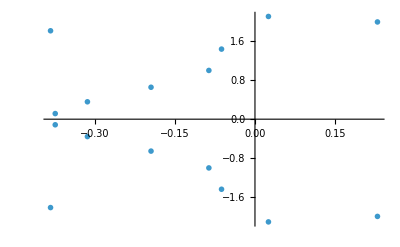

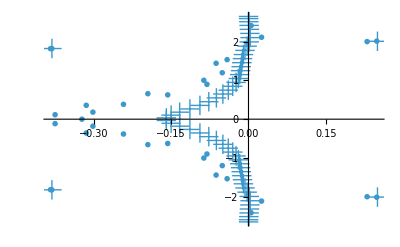

```mathematica
k=21;
LHSNum=(LHS[k]/.coeff)/.barCoeffs;
RHSNum=(RHS[k]/.coeff)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n21=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotMarkers->Style["◯",8]];

k=60;
LHSNum=(LHS[k]/.coeff)/.barCoeffs;
RHSNum=(RHS[k]/.coeff)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n60=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotMarkers->Style["+",20]];

k=16;
LHSNum=(LHS[k]/.coeff)/.barCoeffs;
RHSNum=(RHS[k]/.coeff)/.barCoeffs;
Print[LHSNum];
Print[RHSNum];

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n81=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotMarkers->Style["·",36]]

Show[n21,n60,n81,PlotRange->{All,All}]
```

## Dendro Output

### Hide

```mathematica
derivativeOrder=1;
interiorOrder=n;
totalBoundRows=numBoundaryRows;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList=RHSPars;
interiorParametersValues=interiorCoeffs/.{α->alpha,β->beta};
boundaryParametersValues=boundary/.{α12->gamma01,β12->gamma02,α21->gamma10,α22->gamma12,β22->gamma13,β31->gamma20,α31->gamma21,α32->gamma23,β32->gamma24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13,gamma20,gamma21,gamma23,gamma24};
RHSBoundaryList={a00,a01,a02,a03,a04,a05,a06,a10,a11,a12,a13,a14,a15,a16,a20,a21,a22,a23,a24,a25,a26};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)
```

```mathematica
(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str]
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
]






(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]]
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]]
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]]

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]<>"/"<>ToString[2*i]<>".0"]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]<>"/"<>ToString[2*(i-Length[RHSInteriorList]-1)]<>".0"]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]<>"/"<>ToString[i^2]<>".0"]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]<>"/"<>ToString[(i-Length[RHSInteriorList]-1)^2]<>".0"]]]]]

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
]


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]<>"/"<>ToString[i^2]<>".0"]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>StringDrop[StringDrop[ToString[t1List],1],-1]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
]

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

### Show

```mathematica
outExt="h";
(*Print header*)
Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_P4","_yHat0_",ToString[yHat0],"_yHat1_",ToString[yHat1],"_yHat2_",ToString[yHat2],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]]
```

Dendro-Ready Coefficients (Copied to clipboard):

MatrixDiagonalEntries* BYUDerivsP160R3DiagonalsFirstOrder(
	const std::vector<double>& D_coeffs) {
		double alpha0 = 0.5770460201292381;
		double alpha = alpha0 + D_coeffs[0];

		double beta = 0.08900836845092142;
		double a1 = 0.6517078440898839;
		double a2 = 0.24815882627035918;
		double a3 = 0.006009630649852392;
		double gamma01 = 9.963989489704737;
		double gamma02 = 11.566450096118793;
		double gamma10 = 0.1742795462287032;
		double gamma12 = 0.16936101668959594;
		double gamma13 =  - 0.40635680897387616;
		double gamma20 = 0.024862280752485255;
		double gamma21 = 0.3686413380038592;
		double gamma23 = 0.7547612164814999;
		double gamma24 = 0.14377907331761833;
		double a00 =  - 3.7289097716560913;
		double a01 =  - 11.331495548700467;
		double a02 = 10.060192799902282;
		double a03 = 5.323729074593792;
		double a04 =  - 0.38988258114889796;
		double a05 = 0.07405849575387713;
		double a06 =  - 0.007692468220204209;
		double a10 =  - 0.5727257684096644;
		double a11 =  - 0.41122629803324956;
		double a12 = 1.4956215666978685;
		double a13 =  - 0.3873992442740351;
		double a14 =  - 0.14379120110924926;
		double a15 = 0.022496214935100102;
		double a16 =  - 0.00297526980610778;
		double a20 =  - 0.0988179619140393;
		double a21 =  - 0.631836284848514;
		double a22 =  - 0.3383272813050932;
		double a23 = 0.6887173470201261;
		double a24 = 0.36624370762969716;
		double a25 = 0.01471495607194349;
		double a26 =  - 0.0006944826541200835;

		// boundary elements for P matrix for 1st derivative
		std::vector<std::vector<double>> P1DiagBoundary{
			{1.0, gamma01, gamma02},
			{gamma10, 1.0, gamma12, gamma13},
			{gamma20, gamma21, 1.0, gamma23, gamma24}
		};

		// diagonal elements for P matrix for 1st derivative
		std::vector<double> P1DiagInterior{
			beta, alpha, 1.0, alpha, beta
		};

		// boundary elements for Q matrix for 1st derivative
		std::vector<std::vector<double>> Q1DiagBoundary{
			{a00, a01, a02, a03, a04, a05, a06},
			{a10, a11, a12, a13, a14, a15, a16},
			{a20, a21, a22, a23, a24, a25, a26}
		};

		// diagonal elements for Q matrix for 1st derivative
		std::vector<double> Q1DiagInterior{
			-a3/6.0, -a2/4.0, -a1/2.0, 0.0, a1/2.0, a2/4.0, a3/6.0
		};

		// store the entries for matrix creation
		MatrixDiagonalEntries* diagEntries = new
			MatrixDiagonalEntries{
				P1DiagInterior, P1DiagBoundary, Q1DiagInterior, Q1DiagBoundary
			};
		return diagEntries;
	}

Saved to file: BYU_P6_yHat0_1.89_yHat1_0.99_yHat2_0.2.h